## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
SetDirectory[NotebookDirectory[]]
rxnName="TKT1";
```

/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1

```mathematica
Import["../../EnzymeBuildingBlocks/initializeNotebook.m"]
```

working dir:/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/

## Import Data From Database

```mathematica
desiredComplex=6355;
Import["../../EnzymeBuildingBlocks/importFromDB.m"]
```

unique_name | id
TRANSKETOI-CPLX | 6355

First::nofirst: {} has a length of zero and no first element.

Rest::norest: Cannot take Rest of expression {} with length zero.

JDBC::error: "ERROR: syntax error at or near \"{\"\n  Position: 45"

## Construct Module and Set Up Comparison Equations

### Print Module Dependent Information

```mathematica
(*Print Available Reaction/Protein Data*)
rxn
bindingMech[[1,8;;9]]//TableForm
#[[3;;4]]&/@complexData[[1]]//TableForm

(*Print Available Kinetic Data*)
{{"Km Values:","(kmList)"},
{"Substrate","Km_Value","CoSubstrate","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~kmList//TableForm
{{"S0.5 Values:","(s05List)"},
{"Substrate","S0.5_Value","CoSubstrate","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~s05List//TableForm
{{"kcat Values:","(kcatList)"},
{"Metabolite(s)","Value","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~kcatList//TableForm
{{"Inhibition Values:","(inhibitionList)"},
{"Parameter_Type","Inhibitor","Value","Inhibition Type","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~inhibitionList//TableForm
{{"Activation Values:","(activationList)"},
{"Parameter_Type","Activator","Value","Activation Type","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~activationList//TableForm
{{"Other Parameters:","(otherParms)"},
{"Parameter_Type","Metabolite","Value","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~otherParms//TableForm
```

(r5p^c+(xu5p-D)^c⇌g3p^c+s7p^c)^TKT1

Ping Pong Bi Bi
"[xu5p-D,g3p,r5p,s7p],[xu5p-D,g3p,e4p,f6p]"

Structure | 2
Active Sites | 2

Km Values: | (kmList) |  |  |  |  |  | 
Substrate | Km_Value | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
xu5p-D | 0.00016 | thmpp | 0.001
e4p | 0.009 | M | 8.5 | 30. | glygly | 0.05 | mg2 | 0.005
cl | 0.01
r5p | 0.0014 | thmpp | 0.001
xu5p-D | 0.016 | M | 8.5 | 30. | glygly | 0.05 | mg2 | 0.005
cl | 0.01
e4p | 0.00009 | thmpp | 0.001
xu5p-D | 0.016 | M | 8.5 | 30. | glygly | 0.05 | mg2 | 0.005
cl | 0.01
g3p | 0.0021 | thmpp | 0.001
xu5p-D | 0.016 | M | 8.5 | 30. | glygly | 0.05 | mg2 | 0.005
cl | 0.01
f6p | 0.0011 | thmpp | 0.001
gcald | 1.4 | M | 8.5 | 30. | glygly | 0.05 | mg2 | 0.005
cl | 0.01
s7p | 0.004 | thmpp | 0.001
e4p | 0.009 | M | 8.5 | 30. | glygly | 0.05 | mg2 | 0.005
cl | 0.01

S0.5 Values: | (s05List) |  |  |  |  |  | 
Substrate | S0.5_Value | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values: | (kcatList) |  |  |  |  | 
Metabolite(s) | Value | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
gcald | Null
hpyr | Null | 84.6 | 1/S | Null | Null |  |

Inhibition Values: | (inhibitionList) |  |  |  |  |  |  | 
Parameter_Type | Inhibitor | Value | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values: | (activationList) |  |  |  |  |  |  | 
Parameter_Type | Activator | Value | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters: | (otherParms) |  |  |  |  |  | 
Parameter_Type | Metabolite | Value | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
Kd | mg2 | 0.000036 | M | 8.5 | 30. | glygly | 0.05 | 
Kd | thmpp | 0.000029 | M | 8.5 | 30. | glygly | 0.05 |

### Construct enzyme module

```mathematica
rxn
```

(r5p^c+(xu5p-D)^c⇌g3p^c+s7p^c)^TKT1

```mathematica
{{"Ping Pong Bi Bi"}, {"\"[xu5p-D,g3p,r5p,s7p],[xu5p-D,g3p,e4p,f6p]\""}}
```

```mathematica
catalyticBranch={"E_TKT1[c] + xu5p-D[c] <=> E_TKT1[c]&xu5p-D",
				"E_TKT1[c]&xu5p-D <=> E_TKT1[c]&g3p",
				"E_TKT1[c]&g3p <=> E_TKT1[c] + g3p[c]",

				"E_TKT1[c] + r5p[c] <=> E_TKT1[c]&r5p",
				"E_TKT1[c]&r5p <=> E_TKT1[c]&s7p",
				"E_TKT1[c]&s7p <=> E_TKT1[c] + s7p[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
```

#### Visualize Module (Optional)

{((TKT1^c)_^+r5p^c⇌(TKT1^c&r5p^c)_^)^TKT11,((TKT1^c)_^+(xu5p-D)^c⇌(TKT1^c&(xu5p-D)^c)_^)^TKT12,((TKT1^c&s7p^c)_^⇌(TKT1^c)_^+s7p^c)^TKT13,((TKT1^c&r5p^c)_^⇌(TKT1^c&s7p^c)_^)^TKT14,((TKT1^c&g3p^c)_^⇌(TKT1^c)_^+g3p^c)^TKT15,((TKT1^c&(xu5p-D)^c)_^⇌(TKT1^c&g3p^c)_^)^TKT16}

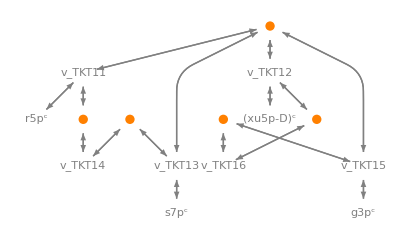

```mathematica
enzymeModel["Reactions"]
visualizePathways[enzymeModel](*Caution: Graphics can be unstable*)
enzymeModel;
```

### Setup King-Altmann Equations

#### Import and Define Dependencies

```mathematica
rNonModelMets[metList_]:=Delete[Delete[metList,Position[metList,h^c]],Position[metList,h2o^c]];(*h^c and h2o^c are not modeled*)
reverseZeroSub=#->0&/@rNonModelMets[getProducts[rxn]];
forwardZeroSub=#->0&/@rNonModelMets[getSubstrates[rxn]];
metSatForSub=#->∞&/@rNonModelMets[getSubstrates[rxn]];
metSatRevSub=#->∞&/@rNonModelMets[getProducts[rxn]];
rates=enzymeModel["Rates"]/.elem_[t]:>elem;
enzName=enzymeModel["Enzymes"][[1]]//getID//ToString;
KeqName=rxnName//ToString;
KeqVal=Keq[KeqName];
competitiveRxns={};(*Initialization for later. Do not modify this*)
eqRateConstSub={};(*Initialization for later. Do not modify this*)

(*You could modify these, but you shouldn't unless you run into problems*)
volumeSub={parameter["Volume","c"]->1};
lowerParamBound=-6;
upperParamBound=9;
simplifyMaxTime=1*^-5;
```

#### Extract Transition ID from Mass Action Equations and Separate Catalytic and Non-Catalytic Reactions

The transition indices are extracted based off of the sum of their mass action stoichiometry. Reactions with a sum of zero are assumed to be catalytic.

```mathematica
(*Initialize Lists*)
transitionID={};
allCatalyticReactions={};(*All Catalytic Reactions*)
nonCatalyticReactions={};(*All Other Reactions*)

(*Separate Catalytic and Non-Catalytic Reactions*)
If[StringMatchQ[#[[1]],RegularExpression[enzName<>"\\d+.*"]],(*If Reaction Name == "The Enzyme Name"<>+"A Number"*)
(*True: Reaction is Catalytic*)
AppendTo[allCatalyticReactions,#],
(*False: Reaction is Not Catalytic*)
AppendTo[nonCatalyticReactions,#]
]&/@enzymeModel["Reactions"];

(*Identify Transition Rate Equations*)
sumReactionStoich=Table[Total[getSignedStoich[allCatalyticReactions[[eqn]]]],{eqn,Length[allCatalyticReactions]}];
Do[If[sumReactionStoich[[eqn]] ==0,transitionID=Append[transitionID,allCatalyticReactions[[eqn]]//getID]],{eqn,Length[sumReactionStoich]}];

(*Extract Transition Rate Equations*)
transitionRateEqs={};
If[
MemberQ[transitionID,getID[Cases[#,_Keq,∞][[1]]]],
AppendTo[transitionRateEqs,#]
]&/@rates;
```

(*Double Check This Result*)

```mathematica
enzymeModel["Reactions"]
(*enzymeModel["Reactions"][[#]]&/@transitionID;*)
```

{((TKT1^c)_^+r5p^c⇌(TKT1^c&r5p^c)_^)^TKT11,((TKT1^c)_^+(xu5p-D)^c⇌(TKT1^c&(xu5p-D)^c)_^)^TKT12,((TKT1^c&s7p^c)_^⇌(TKT1^c)_^+s7p^c)^TKT13,((TKT1^c&r5p^c)_^⇌(TKT1^c&s7p^c)_^)^TKT14,((TKT1^c&g3p^c)_^⇌(TKT1^c)_^+g3p^c)^TKT15,((TKT1^c&(xu5p-D)^c)_^⇌(TKT1^c&g3p^c)_^)^TKT16}

#### King-Altman Workaround Using Mathematica Solve Without Product Inhibition

This section of code will check to see if there is a 'absoluteFluxNoProdInhib.m' file in the notebook directory from a previous cell evalution, and it will either derive a generalized flux equation without competitive product inhibition (may take a long time) or import the previously derived flux equation. Note: If you modify the binding mechanism used in the constructEnzymeModule or manually add additional reactions to the model, you should delete the ‘absoluteFluxNoProdInhib.m’ file in this notebook’s current directory.

```mathematica
unifiedRateConstList=Flatten[{rateconst[getID[#],True]->unifyRateConstants[rateconst[getID[#],True]],rateconst[getID[#],False]->unifyRateConstants[rateconst[getID[#],False]]}&/@allCatalyticReactions];
unifiedRateConstList=Join[unifiedRateConstList,Flatten[{rateconst[getID[#],True]->unifyRateConstants[rateconst[getID[#],True]],rateconst[getID[#],False]->unifyRateConstants[rateconst[getID[#],False]]}&/@nonCatalyticReactions]];
```

```mathematica
If[
FileExistsQ[workingDir<>"enzSolNoProdInhib.m"]&&FileExistsQ[workingDir<>"absoluteFluxNoProdInhib.m"],
(*True: 'enzSolNoProdInhib.m' and 'absoluteFluxNoProdInhib.m' Exists*)
enzSolNoProdInhib=Import[workingDir<>"enzSolNoProdInhib.m"];
absoluteFluxNoProdInhib=Import[workingDir<>"absoluteFluxNoProdInhib.m"];,

(*False: 'enzSolNoProdInhib.m' and 'absoluteFluxNoProdInhib.m'  Do Not Exist*)
	(*Generate a System of Equations *)
fluxEq=(*unifyRateConstants[*)Total[transitionRateEqs];
fluxEq=keq2kHT[fluxEq]/.unifiedRateConstList(*]*);(*Flux Will Always Go through the Transition Step*)
enzForms=Cases[enzymeModel["Species"],_enzyme]//Union;
enzConservationEq=parameter["E_total"]==Total[enzForms];(*Enzyme Conservation Equation*)
enzPos=Flatten[Position[enzymeModel["Species"],_enzyme]];
ssEq=stripTime[enzymeModel["ODE"][[enzPos]]/._'[t]->0];(*Steady State Equations*)
ssEq=(*unifyRateConstants[*)keq2kHT[ssEq]/.unifiedRateConstList(*]*);

	(*Solve the System for Each Enzyme Form (This May Take Some Time)*)
enzSolNoProdInhib=anonymize[Solve[Join[ssEq,{enzConservationEq}],enzForms]];
enzSolNoProdInhib=keq2kHT[enzSolNoProdInhib[[1]]];

	(*Apply the Solution to the Flux Equation*)
absoluteFluxNoProdInhib=fluxEq/.enzSolNoProdInhib;(*In terms of E_total*)
absoluteFluxNoProdInhib=parameter["v",rxnName]->keq2kHT[
													anonymize[Simplify[
													absoluteFluxNoProdInhib
													]]
													];

	(*Cache the Results*)
Export[workingDir<>"enzSolNoProdInhib.m",enzSolNoProdInhib];
Export[workingDir<>"absoluteFluxNoProdInhib.m",absoluteFluxNoProdInhib];
];
```

```mathematica
Semi-Automated Add Competitive Inhibition Steps
```

```mathematica
(*
This block of code assembles competitive inhibition reactions to be added to the model. The reactions are appended to the 
'competitiveRxns' list, initialized above. Copy this cell for each competitive inhibitor you want to add. The reactions in 
'competitiveRxns' are added to the Enzyme Module, 'enzymeModel', in a separate cell below.
*)

(*USER INPUT----------------------------------------*)
inhibitorMet={};
affectedMets={};(*There can be multiple metabolites*)
(*-------------------------------------------------*)

affectedRxns=Table[Select[allCatalyticReactions,MemberQ[Union[{getSubstrates[#],getProducts[#]}]~Flatten~1,met]&],{met,affectedMets}];
affectedEnzForms=Table[
If[
MemberQ[getSubstrates[rxn],affectedMets[[met]]],
(*True: Is a Reactant*)
#&/@Cases[getSubstrates[rxn],_enzyme,∞],
(*False: Is a Product*)
#&/@Cases[getProducts[rxn],_enzyme,∞]
],
{met,affectedMets//Length},{rxn,affectedRxns[[met]]}]//Flatten;

AppendTo[competitiveRxns,
Table[
r[enzName<>"_Competitive_"<>inhibitorMet[[1]]<>"_"<>ToString[enz],(*Reaction Name*)
{affectedEnzForms[[enz]],inhibitorMet},(*Substrates*)
{bindCatalytic[affectedEnzForms[[enz]],inhibitorMet]},(*Products*)
{1,1,1}](*Stoichiometry*),
{enz,affectedEnzForms//Length}]];
```

```mathematica
(*Evaluate This Cell*)
(*Equivalent Rate Constants*)
eqRateConstSub=Join[eqRateConstSub,rateconst[getID[#],True]->
rateconst[StringCases[getID[#],RegularExpression["(.*)_\\d+"]->"$1"][[1]],True]&/@
Flatten[competitiveRxns]]//Union;
eqRateConstSub=Join[eqRateConstSub,rateconst[getID[#],False]->
rateconst[StringCases[getID[#],RegularExpression["(.*)_\\d+"]->"$1"][[1]],False]&/@
Flatten[competitiveRxns]]//Union;
```

```mathematica
(*Add Competitive Reactions to the Enzyme Module*)
enzymeModel=addReactions[enzymeModel,Flatten[competitiveRxns]];
nonCatalyticReactions=Join[nonCatalyticReactions,competitiveRxns]//Flatten;
(*Print Reactions*)
enzymeModel["Reactions"]
```

{((PFK1^c)_^+f6p^c⇌(PFK1^c&f6p^c)_^)^PFK11,((PFK1^c&fdp^c)_^⇌(PFK1^c)_^+fdp^c)^PFK12,((PFK1^c&f6p^c)_^+atp^c⇌(PFK1^c&f6p^c&atp^c)_^)^PFK13,((PFK1^c&fdp^c&adp^c)_^⇌(PFK1^c&fdp^c)_^+adp^c)^PFK14,((PFK1^c&f6p^c&atp^c)_^⇌(PFK1^c&fdp^c&adp^c)_^)^PFK15,((PFK1^c)_^(gdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^c))^PFK11$3,((PFK1^c&fdp^c)_^(gdp^c)⇌(PFK1^c)_^(gdp^c)+fdp^c)^PFK12$3,((PFK1^c&f6p^c)_^(gdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^c))^PFK13$3,((PFK1^c&fdp^c&adp^c)_^(gdp^c)⇌(PFK1^c&fdp^c)_^(gdp^c)+adp^c)^PFK14$3,((PFK1^c&f6p^c&atp^c)_^(gdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^c))^PFK15$3,((PFK1^c)_^(gdp^cgdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^cgdp^c))^PFK11$7,((PFK1^c&fdp^c)_^(gdp^cgdp^c)⇌(PFK1^c)_^(gdp^cgdp^c)+fdp^c)^PFK12$7,((PFK1^c&f6p^c)_^(gdp^cgdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^c))^PFK13$7,((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c)⇌(PFK1^c&fdp^c)_^(gdp^cgdp^c)+adp^c)^PFK14$7,((PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c))^PFK15$7,((PFK1^c)_^(gdp^cgdp^cgdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c))^PFK11$8,((PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c)⇌(PFK1^c)_^(gdp^cgdp^cgdp^c)+fdp^c)^PFK12$8,((PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^c))^PFK13$8,((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c)+adp^c)^PFK14$8,((PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c))^PFK15$8,((PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c)+f6p^c⇌(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK11$10,((PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c)⇌(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c)+fdp^c)^PFK12$10,((PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c)+atp^c⇌(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK13$10,((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c)+adp^c)^PFK14$10,((PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK15$10,((PFK1^c)_^+gdp^c⇌(PFK1^c)_^(gdp^c))^PFK1_Activation_gdp$11,((PFK1^c)_^(gdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^c))^PFK1_Activation_gdp$12,((PFK1^c)_^(gdp^cgdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^cgdp^c))^PFK1_Activation_gdp$13,((PFK1^c)_^(gdp^cgdp^cgdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK1_Activation_gdp$14,((PFK1_T^c)_^+pep^c⇌(PFK1_T^c)_(pep^c)^)^PFK1_Inhibition_pep$15,((PFK1_T^c)_(pep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^c)^)^PFK1_Inhibition_pep$16,((PFK1_T^c)_(pep^cpep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^cpep^c)^)^PFK1_Inhibition_pep$17,((PFK1_T^c)_(pep^cpep^cpep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^cpep^cpep^c)^)^PFK1_Inhibition_pep$18,((PFK1^c)_^⇌(PFK1_T^c)_^)^PFK1_TransitionStep,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Competitive_adp_1,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Competitive_adp_2,((PFK1^c&f6p^c)_^(gdp^cgdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^cgdp^c))^PFK1_Competitive_adp_3,((PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^cgdp^cgdp^c))^PFK1_Competitive_adp_4,((PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK1_Competitive_adp_5}

#### King-Altman Workaround Using Mathematica Solve

This section of code will check to see if there is a 'absoluteFlux.m' file in the notebook directory from a previous cell evalution, and it will either derive a generalized flux equation (may take a long time) or import the previously derived flux equation. Note: If you modify the binding mechanism used in the constructEnzymeModule or manually add additional reactions to the model, you should delete the ‘absoluteFlux.m’ file in this notebook’s current directory.

```mathematica
If[FileExistsQ[workingDir<>"enzSol.m"]&&FileExistsQ[workingDir<>"absoluteFlux.m"],
(*True: 'enzSol.m' and 'absoluteFlux.m' Exists*)
enzSol=Import[workingDir<>"enzSol.m"];
absoluteFlux=Import[workingDir<>"absoluteFlux.m"];,

(*False: 'enzSol.m' and 'absoluteFlux.m'  Do Not Exist*)
	(*Generate a System of Equations *)
fluxEq=(*unifyRateConstants[*)Total[transitionRateEqs]/.unifiedRateConstList(*]*);(*Flux Will Always Go through the Transition Step*)
enzForms=Cases[enzymeModel["Species"],_enzyme]//Union;
enzConservationEq=parameter["E_total"]==Total[enzForms];(*Enzyme Conservation Equation*)
enzPos=Flatten[Position[enzymeModel["Species"],_enzyme]];
ssEq=stripTime[enzymeModel["ODE"][[enzPos]]/._'[t]->0];(*Steady State Equations*)
ssEq=(*unifyRateConstants*)keq2kHT[ssEq]/.unifiedRateConstList;

	(*Solve the System for Each Enzyme Form (This May Take Some Time)*)
enzSol=anonymize[Solve[Join[ssEq,{enzConservationEq}],enzForms]];
enzSol=keq2kHT[enzSol[[1]]];

	(*Apply the Solution to the Flux Equation*)
absoluteFlux=fluxEq/.enzSol;(*In terms of E_total*)
absoluteFlux=parameter["v",rxnName]->keq2kHT[
											anonymize[Simplify[
											absoluteFlux
											]]
											];

	(*Cache the Results*)
Export[workingDir<>"enzSol.m",enzSol];
Export[workingDir<>"absoluteFlux.m",absoluteFlux];
];
```

#### Equivalent Rate Constant Substitution for Random Ordered Mechanisms

This should work automatically, a substitution rule list is created with the name: ‘eqRateConstSub’. It is kind of a greedy section of code, so double check the results to make sure they’re accurate

```mathematica
(*Work Around for Added Competitive Reaction ID's*)
eqIDSub=Union[getID[#[[1]]]->getID[#[[2]]]&/@eqRateConstSub];

(*Catalytic Reactions*)
freeMetRxns=Cases[getSpecies[#],_metabolite,∞]&/@allCatalyticReactions;
allSubstrates=Cases[getSpecies[enzymeModel],_metabolite,∞];
equivalentRxns={};
Do[
AppendTo[equivalentRxns,{}],
{Length[allSubstrates]}];
(*Extract Equivalent Reactions*)
Table[
If[
SameQ[freeMetRxns[[rxn,1]],allSubstrates[[met]]],
AppendTo[equivalentRxns[[met]],rxn]];
freeMetRxns[[rxn,1]],
{met,Length[allSubstrates]},{rxn,Length[freeMetRxns]}]~Quiet~{Part::partw};
(*Parallel Catalytic Reactions Are Not Dealt with Using this Rule List*)
equivalentRxns=Table[{unifyRateConstants[getID[allCatalyticReactions[[#]]]],#}&/@rxnSet,{rxnSet,equivalentRxns}];
equivalentRxns=Table[
If[Length[DeleteDuplicates[rxnSet,#1[[1]]==#2[[1]]&]]>1,
DeleteDuplicates[rxnSet,#1[[1]]==#2[[1]]&][[All,2]],
{}
],
{rxnSet,equivalentRxns}];
(*Assemble Rule List and New 'rateconst' Names*)
equivalentRxnIDs=Table[
ToString[enzName]<>ToString[equivalentRxns[[eqSet,react]]],
{eqSet,Length[equivalentRxns]},{react,Length[equivalentRxns[[eqSet]]]}];
eqRateConst=Table[
StringJoin[Riffle[Map[ToString,Join[{enzName},equivalentRxns[[eqRxn]]]],"_"]],
{eqRxn,Length[equivalentRxns]}];
eqRateConst=Table[
rateconst[rate,If[boole==1,False,True]],
{rate,eqRateConst},{boole,2}];
indvRateConst=Table[
rateconst[equivalentRxnIDs[[eqSet,reactID]],If[boole==1,False,True]],
{eqSet,Length[equivalentRxnIDs]},{boole,2},{reactID,Length[equivalentRxnIDs[[eqSet]]]}];
eqRateConstSub=Join[eqRateConstSub,Flatten[
Table[
#->eqRateConst[[eqRate,direction]]&/@indvRateConst[[eqRate,direction]],{eqRate,Length[eqRateConst]},{direction,Length[eqRateConst[[eqRate]]]}]
]];

(*Non-Catalytic Reactions*)
freeMetRxns=Cases[getSpecies[#],_metabolite,∞]&/@nonCatalyticReactions;
allSubstrates=Cases[getSpecies[enzymeModel],_metabolite,∞];
equivalentRxns={};
Do[
AppendTo[equivalentRxns,{}],
{Length[allSubstrates]}];
(*Extract Equivalent Reactions*)
Table[
If[
SameQ[freeMetRxns[[rxn,1]],allSubstrates[[met]]],
AppendTo[equivalentRxns[[met]],rxn]];
freeMetRxns[[rxn,1]],
{met,Length[allSubstrates]},{rxn,Length[freeMetRxns]}]~Quiet~{Part::partw};
(*Parallel Catalytic Reactions Are Not Dealt with Using this Rule List*)
equivalentRxns=Table[{unifyRateConstants[getID[nonCatalyticReactions[[#]]]],#}&/@rxnSet,{rxnSet,equivalentRxns}]/.eqIDSub;
equivalentRxns=Table[
If[Length[DeleteDuplicates[rxnSet,#1[[1]]==#2[[1]]&]]>1,
DeleteDuplicates[rxnSet,#1[[1]]==#2[[1]]&][[All,2]],
{}
],
{rxnSet,equivalentRxns}];
(*Assemble Rule List and New 'rateconst' Names*)
equivalentRxnIDs=Table[
ToString[enzName]<>ToString[equivalentRxns[[eqSet,react]]],
{eqSet,Length[equivalentRxns]},{react,Length[equivalentRxns[[eqSet]]]}];
eqRateConst=Table[
StringJoin[Riffle[Map[ToString,Join[{enzName},equivalentRxns[[eqRxn]]]],"_"]],
{eqRxn,Length[equivalentRxns]}];
eqRateConst=Table[
rateconst[rate,If[boole==1,False,True]],
{rate,eqRateConst},{boole,2}];
indvRateConst=Table[
rateconst[equivalentRxnIDs[[eqSet,reactID]],If[boole==1,False,True]],
{eqSet,Length[equivalentRxnIDs]},{boole,2},{reactID,Length[equivalentRxnIDs[[eqSet]]]}];
eqRateConstSub=Join[eqRateConstSub,Flatten[
Table[
#->eqRateConst[[eqRate,direction]]&/@indvRateConst[[eqRate,direction]],{eqRate,Length[eqRateConst]},{direction,Length[eqRateConst[[eqRate]]]}]
]]//Union;
```

#### Assemble the Generalized Flux Equation and Derive a Substition of the Reverse Catalytic Rate Constant Using the Haldane Relation

```mathematica
absoluteFluxEqn=absoluteFlux[[2]];
absoluteFluxEqn=absoluteFluxEqn/.unifiedRateConstList/.eqRateConstSub;(*Equivalent Rate Constants*)

haldane=(*unifyRateConstants[*)haldaneRelation[KeqName,allCatalyticReactions]/.unifiedRateConstList;
haldaneSubOutParameter=Table[Select[reverseConsts[enzymeModel],getID[#]==id&],{id,transitionID}]//Flatten;
haldaneSub=Quiet[Solve[haldane/.{haldane[[1]]->KeqVal},haldaneSubOutParameter[[1]]][[1]],{Solve::ratnz}];
haldaneSub=haldaneSub/.eqRateConstSub;(*Equivalent Rate Constants*)
```

#### Assemble Kinetic MASS Action Comparision Equations that Match to Km and kcat Data

Simplify fixes Python evaluation issues dealing with fractional exponents (e.g. ‘(-1)**(3/5)’ returns 1.0)

```mathematica
(*kcat Forward*)
absoluteRateForward=
Simplify[(absoluteFluxEqn/.reverseZeroSub/.volumeSub)];

(*kcat Reverse*)
absoluteRateReverse=
Simplify[(-absoluteFluxEqn/.forwardZeroSub/.volumeSub)];

(*Forward Km(s)*)
relativeRateForward=
Simplify[absoluteRateForward/(Limit[absoluteFluxEqn/.reverseZeroSub/.volumeSub,#])]&/@metSatForSub;
(*Reverse Km(s)*)
relativeRateReverse=
Simplify[-absoluteRateReverse/(Limit[absoluteFluxEqn/.forwardZeroSub/.volumeSub,#])]&/@metSatRevSub;
```

#### Assemble Rate Constant And Metabolite Substitutions for Export

```mathematica
finalRateConsts=
Variables[
Union[
Cases[
Join[{absoluteRateForward},{absoluteRateReverse},relativeRateForward,relativeRateReverse]//Flatten,
_rateconst,∞]]];
rateConstsSub=Thread[finalRateConsts->Table["x<"<>ToString[i]<>">",{i,0,Length[finalRateConsts]-1}]];

(*Extract All Metabolites*)
mets=Table[
{param[[7]],Select[param[[15]],#[[5]]≠"Buffer"&&#[[5]]≠"Salt"&&#[[5]]≠"Cofactor"&][[All,3]]},
{param, parameterData}]//Flatten//Union;
mets=Select[mets,#≠"Null"&];
char2met=#->m[#,"c"]&/@mets;
mets=mets/.char2met;
metsFull=Join[mets,Cases[enzymeModel,_metabolite,∞]]//Union;

(*Handle Metabolites for Export*)
finalMets=Join[metsFull,{Underscript[E_total, Global],parameter["pH"],parameter["Temp"]}];
finalMets=Prepend[finalMets,KeqVal];
metsSub=
Thread[finalMets->Table["d<"<>ToString[i]<>">",{i,0,Length[finalMets]-1}]];
```

### Manual Modifications Section

This section provides a space to manually modify your kinetic equations before they are exported.

#### None

### Export Equations

```mathematica
eqnNameList={"absRateFor",
			"absRateRev",
			Table["relRateFor_"<>ToString[satMet],{satMet,metSatForSub[[All,1,1]]}],
			Table["relRateRev_"<>ToString[satMet],{satMet,metSatRevSub[[All,1,1]]}]}//Flatten;

eqnValList={absoluteRateForward,
			absoluteRateReverse,
			Table[eqn,{eqn,relativeRateForward}],
			Table[eqn,{eqn,relativeRateReverse}]}//Flatten;

eqnValListPy=Table[eqn/.rateConstsSub/.metsSub//ToPython,{eqn,eqnValList}];

eqnList={eqnNameList,eqnValListPy,eqnValList};
fileList=Table[outputPath<>eqnname<>".txt",{eqnname,eqnList[[1]]}];
fileListSub=Table[fileList[[i]]->eqnValList[[i]],{i,1,Length[fileList]}];
Do[Export[fileList[[i]],eqnList[[2,i]]],{i,1,Length[eqnList[[2]]]}];
```

## Semi-Automated Simulate Data

### User Input Section

```mathematica
minPsDataVal[Km_]:=Log10[Km]-1;
maxPsDataVal[Km_]:=Log10[Km]+1;
logStepSize=0.2;
(*nonKmParamWeight=3;*)
nonKmParamWeight=Length[Table[1,{i,minPsDataVal[1],maxPsDataVal[1],logStepSize}]];(*Weighting factor for non-Km data points. You can be specify this manually*)
eTotal=1;(*Enzyme Total, Should Be 1 for Fitting*)
assumedSaturatingConc=0.01 ;(*in Molarity*)

(*Chemical Activity Correction Options*)
inVivoPH=7.5;(*Assumed in vivo pH*)
inVivoIS=0.25;(*Assumed in vivo Ionic Strength, in Molarity*)
effectiveIonDiameter=3;(*Used in Debye-Huckel equation, in Angstroms*)

(*Initialization of Chemical Activity Correction. These values represent no correction (i.e. Chemical Activity is just the Metabolite Concentration)*)
activeIsoSub=Thread[metsFull->metsFull];(*[S^z] = [S] *)
activityCoefficient=Thread[metsFull->1];(* γ = 1 *)
(**)
```

### Chemical Activity Correction (Optional)

If you want to use the actual metabolite concentrations for fitting and do not want to correct for chemical activities, SKIP THIS SECTION.
--This section of code uses eQuilibrator Data to assmeble equations that calculate the active charge-isomers concentrations for each metabolite based on assay conditions and the chemical activity coefficient.
--The overall chemical activity is calculated by this correction: γ * [S^z], where γ = chemical activity coefficient and [S^z] = the concentration of the active charge form of the metabolite. Skipping this section results in γ = 1 and [S^z] = [S]

#### Extract Data From eQuilibrator and Assemble/Handle Dependencies

This Cell extracts the thermodynamic dependencies from eQuilibrator and configures the variables and substitutions to calculate the charge-isomer concentrations of metabolites (e.g atp4-, atp3-, atp2- ...) and the chemical activity coefficient γ.

```mathematica
(*Pseudo Query Equilibrator for Metabolite Data*)
equilibratorInfo=Table[Select[bigg2equilibrator,getID[#[[1]]]==getID[met]&][[1]],{met,metsFull}];

(*Process the Equilibrator Data*)
equilibratorInfo=Table[
Sort[(*Sort by least to greatest nH*)
DeleteDuplicates[(*Delete by duplicate nH values (Preference is given to Alberty because it is first)*)
Flatten[equilibratorInfo[[met,2,All,3,2]],1],
#1[[2,2]]==#2[[2,2]]&],
#1[[2,2]]<#2[[2,2]]&],
{met,equilibratorInfo//Length}];
equilibratorInfo=Thread[metsFull->equilibratorInfo];
isomerMets=Table[(*Name the Pseudo-Isomers*)
m[getID[metsFull[[met]]]<>"("<>ToString[equilibratorInfo[[met,2,z,5,2]]]<>")","c"],
{met,Length[equilibratorInfo]},{z,Length[equilibratorInfo[[met,2]]]}];
nHSub=Table[
"nH_"<>getID[isomerMets[[met,z]]]->equilibratorInfo[[met,2,z,2,2]],
{met,Length[equilibratorInfo]},{z,Length[equilibratorInfo[[met,2]]]}];
chargeSub=Table[
"z_"<>getID[isomerMets[[met,z]]]->equilibratorInfo[[met,2,z,5,2]],
{met,Length[equilibratorInfo]},{z,Length[equilibratorInfo[[met,2]]]}];
isomerChargeSub=Table[
Thread[isomerMets[[met]]->chargeSub[[met,All,2]]],
{met,isomerMets//Length}];
(*Metabolite Related Thermodynamic Parameters Assembly*)
dGFormationVars=Table[
dGstd["f_"<>getID[isomerMets[[met,z]]]],
{met,Length[isomerMets]},{z,Length[isomerMets[[met]]]}];
dGFormationAdjustedVars=Table[
dGstd["f'_"<>getID[isomerMets[[met,z]]]],
{met,Length[isomerMets]},{z,Length[isomerMets[[met]]]}];
dGFormationVals=Table[(*From Equilibrator*)
If[equilibratorInfo[[met,2,z,1,2]]==0,
(*True: Database Value is zero (i.e. does not have units)*)
dGFormationVars[[met,z]]->equilibratorInfo[[met,2,z,1,2]],
(*False: Database Value is not zero (i.e. has units)*)
dGFormationVars[[met,z]]->equilibratorInfo[[met,2,z,1,2,1]]
],
{met,Length[isomerMets]},{z,Length[isomerMets[[met]]]}];

(*dGFormationVals=Table[(*From Equilibrator*)
dGFormationVars[[met,z]]->equilibratorInfo[[met,2,z,1,2,1]],
{met,Length[isomerMets]},{z,Length[isomerMets[[met]]]}];*)

(* The adjusted delta_G of formation is represented by the following equation:
Subscript[ΔG, f'_j]^∘ = Subscript[ΔG, Subscript[f, j]]^∘ + Subscript[nH, j]*R*T*ln(10)*pH - (2.91482*(Subscript[Z, j] - Subscript[nH, j])*I^(1/2))/(1 +1.6*I^(1/2)),
	where: Subscript[nH, j] = Number of hydrogen atoms in species j  ;
			Subscript[Z, j] = Charge number of species j  ;
			R = 8.314472 Joule Kelvin^-1 Mole^-1  ;
			T = 298.15 Kelvin  ;
			I = Ionic Strength  ;
*)
dGFormationAdjustedVarsSub=Table[
dGFormationAdjustedVars[[met,charge]]-> 
dGFormationVars[[met,charge]]+nHSub[[met,charge,1]]*MolarGasConstant[[1]]*298.15*Log[10]*parameter["pH"]-(2.91482*(chargeSub[[met,charge,1]]^2-nHSub[[met,charge,1]])*parameter["IonicStrength"]^(1/2)/(1+1.6*parameter["IonicStrength"]^(1/2))),
{met,Length[isomerMets]},{charge,Length[isomerMets[[met]]]}];
(*Keq Related Thermodynamic Parameters Assembly*)
(*Keq Variable Names*)
isomerKeqVars=Table[
Keq[getID[metsFull[[met]]]<>"("<>ToString[equilibratorInfo[[met,2,z-1,5,2]]]<>"<=>"<>ToString[equilibratorInfo[[met,2,z,5,2]]]<>")"],{met,Length[equilibratorInfo]},{z,2,Length[equilibratorInfo[[met,2]]]}];
(*delta_G reaction Names*)
dGReactions=Table[
dGstd["r_"<>getID[isomerKeqVars[[met,react]]]],
{met,Length[isomerKeqVars]},{react,Length[isomerKeqVars[[met]]]}];
(* 
The reaction delta_G is represented by the following equation:
Subscript[ΔG, r(j-1<=>j)]^∘ = Subscript[ΔG, f'_j]^∘ - Subscript[ΔG, f'_(j - 1)]^∘       
*)
dGReactionsSub=Table[
dGReactions[[met,react]]->dGFormationAdjustedVars[[met,react+1]]-dGFormationAdjustedVars[[met,react]],
{met,Length[dGReactions]},{react,Length[dGReactions[[met]]]}];
(* 
The pseudo-Isomer Keq is represented by the following equation:
Keq = exp(-Subscript[ΔG, r(j-1<=>j)]^∘/(R*T))  ,

     where:  R = 8.314472 Joule Kelvin^-1 Mole^-1  
	T = 298.15 Kelvin  ;
*)
isomerKeqSub=Table[isomerKeqVars[[met,react]]->Exp[(-1*dGReactions[[met,react]])/(298.15*MolarGasConstant[[1]])],{met,Length[isomerKeqVars]},{react,Length[isomerKeqVars[[met]]]}];
```

#### Assemble and Process the Pseudo-Isomer Equations

This cell evaluates the fractional abundance of each charge isomer at in vivo pH and Ionic Strength (Specified in the User Inputs section). The active charge isomer is guessed to be the most abundant form at in vivo conditions

```mathematica
(*Assemble Pseudo Isomer Equations*)
keqEqns=Table[isomerKeqVars[[met,react]]==isomerMets[[met,react+1]]/isomerMets[[met,react]],{met,Length[isomerKeqVars]},{react,Length[isomerKeqVars[[met]]]}];
conservationEqn=Table[{metsFull[[met]]==Total[isomerMets[[met]]]},{met,Length[metsFull]}];
pIsomerEqns=Table[Join[keqEqns[[met]],conservationEqn[[met]]],{met,keqEqns//Length}];

(*Substitute in Corrections and Data Values*)
pIsomerEqnsFull=
Table[
pIsomerEqns[[met]]/.
isomerKeqSub[[met]]/.
	dGReactionsSub[[met]]/.
		dGFormationAdjustedVarsSub[[met]]/.
			dGFormationVals[[met]]/.
				chargeSub[[met]]/.
					nHSub[[met]]/.
						parameter["pH"]->inVivoPH/.
							parameter["IonicStrength"]->inVivoIS/.
								Thread[metsFull->1],
{met,pIsomerEqns//Length}];

(*Solve for the Pseudo Isomer Concentrations*)
inVivoConc=Table[
Quiet[Solve[
pIsomerEqnsFull[[met]],isomerMets[[met]]
],{Solve::ratnz}][[1]],
{met,isomerMets//Length}];

(*Sort Concentrations by Largest to Smallest*)
inVivoConc=Table[Sort[inVivoConc[[met]],#1[[2]]>#2[[2]]&],{met,inVivoConc//Length}];
"Calculated Fraction of in vivo Concentrations:"
inVivoConc
"Estimated Active Forms:"
activeIsomerForms=Thread[metsFull->inVivoConc[[All,1,1]]]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{0., 0., 2.57006×10^8, -8.12408×10^7, 0.}, {0., 6.59968×10^9, -1.75826×10^6, 0., 0.}, {5.82067×10^10, -10575., 0., 0., 0.}, {1., 1., 1., 1., -1.}} may contain significant numerical errors.

Calculated Fraction of in vivo Concentrations:

{{(adp(-3))^c→0.67776,(adp(-2))^c→0.321996,(adp(-1))^c→0.000232309,(adp(-4))^c→0.0000110907,(adp(0))^c→2.22276×10^-7,(adp(-5))^c→3.74885×10^-12,(adp(1))^c→3.12944×10^-12,(adp(2))^c→5.06793×10^-18},{(atp(-3))^c→0.556017,(atp(-4))^c→0.44298,(atp(-2))^c→0.000835352,(atp(-5))^c→0.000161925,(atp(-1))^c→5.01197×10^-6,(atp(0))^c→1.06709×10^-10,(atp(1))^c→6.87006×10^-16,(atp(2))^c→1.60982×10^-22},{(f6p(-2))^c→0.943566,(f6p(-1))^c→0.0557297,(f6p(-3))^c→0.000704269,(f6p(0))^c→1.22036×10^-8,(f6p(-4))^c→4.22396×10^-9,(f6p(-5))^c→1.39529×10^-15},{(fdp(-4))^c→0.867431,(fdp(-3))^c→0.122292,(fdp(-5))^c→0.00595294,(fdp(-2))^c→0.00432447,(fdp(-6))^c→3.41422×10^-8,(fdp(-1))^c→9.50019×10^-9,(fdp(0))^c→2.32793×10^-15},{(gdp(-3))^c→0.559346,(gdp(-2))^c→0.439389,(gdp(-4))^c→0.00124245,(gdp(-1))^c→0.0000219059,(gdp(-5))^c→1.38803×10^-8,(gdp(0))^c→6.2983×10^-11,(gdp(-6))^c→4.69485×10^-15,(gdp(1))^c→4.35013×10^-17},{(pep(-3))^c→0.75977,(pep(-2))^c→0.240166,(pep(-1))^c→0.0000639842,(pep(0))^c→1.16247×10^-11}}

Estimated Active Forms:

{adp^c→(adp(-3))^c,atp^c→(atp(-3))^c,f6p^c→(f6p(-2))^c,fdp^c→(fdp(-4))^c,gdp^c→(gdp(-3))^c,pep^c→(pep(-3))^c}

#### Manually Specify Active Isomer Forms (Optional)

If you know the actual active charge-isomer, you can specify it here. Note: the whole ‘activeIsomerForms’ list needs to be respecified here.

```mathematica
(*activeIsomerForms={adp^c->(adp(-2))^c,atp^c->(atp(-2))^c,f6p^c->(f6p(-2))^c,fdp^c->(fdp(-4))^c,gdp^c->(gdp(-2))^c,pep^c->(pep(-3))^c};*)
```

#### Set Up Equations for Calculating Pseudo-Isomer Concentrations

Equations calculating the concentration of the active charge-isomer are assembled here. Each equation is a function of: Ionic Strength, pH, and metabolite concentration.

```mathematica
(*Substitute in Corrections and Data Values without the in vivo Assumptions*)
pIsomerEqnsSub=
Table[
pIsomerEqns[[met]]/.
isomerKeqSub[[met]]/.
	dGReactionsSub[[met]]/.
		dGFormationAdjustedVarsSub[[met]]/.
			dGFormationVals[[met]]/.
				chargeSub[[met]]/.
					nHSub[[met]],
{met,pIsomerEqns//Length}];
(*Symbolically Solve for the Pseudo-Isomer Forms*)
isoFormEqns=Table[
Solve[pIsomerEqnsSub[[met]],isomerMets[[met]]][[1]],
{met,isomerMets//Length}];
(*Remove the Active Pseudo-Isomer Form*)
isoForm=Table[
Delete[
isoFormEqns[[met]],Position[
isoFormEqns[[met,All,1]],activeIsomerForms[[met,2]]]],
{met,isomerMets//Length}];
(*Substitute the Equations Back into the Conservation Equation*)
activeIsoFormEqns=Table[
pIsomerEqnsSub[[met,-1]]/.isoForm[[met]],
{met,pIsomerEqnsSub//Length}];
(*Equations that Solve for the Active Isoform Concentration*)
activeIsoSub=Table[
Solve[activeIsoFormEqns[[met]],activeIsomerForms[[met,2]]],
{met,activeIsomerForms//Length}]//Flatten;
```

#### Activity Coefficient Calculation Using the Extended Debye-Huckel Equation

γ = (0.5085*z^2*√IonicStrength)/(1 + 0.3281*a*√IonicStrength), where a is the effective diameter of the ion

```mathematica
debyeHuckelEq[z_,a_]:=(0.5085*z^2*Sqrt[parameter["IonicStrength"]])/(1+0.3281*a*Sqrt[parameter["IonicStrength"]]);
(*Assemble Equations*)
chargeVals=Thread[activeIsomerForms[[All,2]]/.Flatten[isomerChargeSub]];
activityCoefficient=
Thread[(* γ values*)
activeIsomerForms[[All,2]]->
Table[
debyeHuckelEq[met,effectiveIonDiameter],
{met,chargeVals}]];
```

### Data For Km’s

```mathematica
(*Michaelis-Menten Equation*)
kmEqn[S_,Km_]:=S/(Km+S);

(*Change Character Metabolite Names Into MASS toolbox Metabolite Notation. 
NOTE: You may have to add some metabolites in for unusual assay conditions*)
kmMetSub=Table[{km[[1]]->m[km[[1]],"c"],coSub[[1]]->m[coSub[[1]],"c"]},{km,kmList},{coSub,km[[3]]}]//Flatten//Union;
char2met={#[[1]]->#&/@getProducts[rxn]}~
Join~{#[[1]]->#&/@getSubstrates[rxn]}~
Join~kmMetSub//Flatten//Union;
kmListFull=kmList/.char2met;(*Converting to metabolite type can cause a recursion error*)
```

```mathematica
(*Parse Km Values Where the Substrate is Not in the Primary Reaction*)
entriesToDelete={};
Do[If[!MemberQ[Union[Cases[rxn,_metabolite,∞]],kmListFull[[km,1]]],otherParms=Append[otherParms,Prepend[kmListFull[[km]],"Km"]]//Union;(*Move Km param to otherParams*)AppendTo[entriesToDelete,{km}];],{km,Length[kmListFull]}];
kmListFull=Delete[kmListFull,entriesToDelete];
```

```mathematica
(*Generate Data Points (An Order of Magnitude Above and Below the Km's)*)
dataRange=Table[{i,km[[2]]},{km,kmListFull},{i,minPsDataVal[km[[2]]],maxPsDataVal[km[[2]]],logStepSize}];

(*Generate Resultant Rates*)
vValues=Table[
kmEqn[10^dataPt[[1]],dataPt[[2]]],
{dataSet,dataRange},{dataPt,dataSet}];

(*Switch Data to Euclidean Space and Append to the Km List*)
dataRange=10^#[[All,1]]&/@dataRange;
kmListFull=Table[Append[kmListFull[[km]],vValues[[km]]],{km,Length[kmListFull]}];

(*Match to Comparision Equations*)
Do[
If[StringMatchQ[path,RegularExpression[".*_"<>kmListFull[[km,1,1]]<>"\\.txt"]],
AppendTo[
kmListFull[[km]],paramOutputPath<>StringCases[path,RegularExpression[outputPath<>"(.*)"]->"$1"]
]],
{km,Length[kmListFull]},{path,fileList}];

(*Handle CoSubstrates*)
dataCoSub=Table[km[[3]],{km,kmListFull}];
kmListFull=ReplacePart[#,3->Table[{met},{met,metsFull}]]&/@kmListFull;

(*Extract CoSubstrates*)
coSubList={};
Do[
If[
(*True: Is a Reactant*)
MemberQ[metSatForSub[[All,1]],km[[1]]],
indicies=Position[metsFull//Flatten,km[[1]]];(*Subject Metabolite Index*)
AppendTo[indicies,Flatten[Position[metsFull//Flatten,#],1]]&/@metSatRevSub[[All,1]];(*Relative Product Indices*)
AppendTo[coSubList,Delete[metsFull//Flatten,indicies]];,
(*False: Is a Product*)
indicies=Position[metsFull//Flatten,km[[1]]];(*Subject Metabolite Index*)
AppendTo[indicies,Flatten[Position[metsFull//Flatten,#],1]]&/@metSatForSub[[All,1]];(*Relative Product Indices*)
AppendTo[coSubList,Delete[metsFull//Flatten,indicies]];
],{km,kmListFull}];
(*Append the Pseudo-Data Concentrations for Substrate*)
Do[
AppendTo[
kmListFull[[km,3,
Position[
kmListFull[[km,3]],kmListFull[[km,1]]
][[1,1]]
]],
dataRange[[km]]],
{km,kmListFull//Length}];

(*Handle CoSubstrate Data*)
dataCoSubFull=
Table[
Which[
(*CoSubstrate is Present in Data and Has a Data Value*)
MemberQ[dataCoSub[[km,All,1]],coSubList[[km,met]]] && NumberQ[Select[dataCoSub[[km]],#[[1]]==coSubList[[km,met]]&][[1,2]]],
	(*Extract CoSubstrate Concentration and Repeat It for Each Data Point*)
	{Select[dataCoSub[[km]],#[[1]]==coSubList[[km,met]]&][[1,1]],
	Table[
	Select[dataCoSub[[km]],#[[1]]==coSubList[[km,met]]&][[1,2]],
	{dataRange[[km]]//Length}]
	},
(*CoSubstrate is Present in Data but Does not Have a Data Value*)
MemberQ[dataCoSub[[km,All,1]],coSubList[[km,met]]] && !NumberQ[Select[dataCoSub[[km]],#[[1]]==coSubList[[km,met]]&][[1,2]]],
	(*Use an Assumed Concentration and Repeat It for Each Data Point*)
	{Select[dataCoSub[[km]],#[[1]]==coSubList[[km,met]]&][[1,1]],
	Table[
	assumedSaturatingConc,
	{dataRange[[km]]//Length}]
	},
(*CoSubstrate is Not Present in Data*)
!MemberQ[dataCoSub[[km,All,1]],coSubList[[km,met]]],
	(*Use an Assumed Concentration and Repeat It for Each Data Point*)
	{coSubList[[km,met]],
	Table[
	assumedSaturatingConc,
	{dataRange[[km]]//Length}]
	}
],
{km,Length[coSubList]},{met,Length[coSubList[[km]]]}];

(*Append All Remaining CoSubstrate Concentrations to 'kmListFull'*)
Do[
Which[
MemberQ[dataCoSubFull[[km]]//Flatten,kmListFull[[km,3,met,1]]],
(*True: Concentration Values from Data*)
kmListFull[[km,3,met]]={kmListFull[[km,3,met,1]],
Select[dataCoSubFull[[km]],#[[1]]==kmListFull[[km,3,met,1]]&][[1,2]]},
(*False: All Concentration Values Zero*)
!MemberQ[dataCoSubFull[[km]]//Flatten,kmListFull[[km,3,met,1]]]&&!MatchQ[kmListFull[[km,3,met,1]],kmListFull[[km,1]]],
(*Non Pseudo-Data Values*)
kmListFull[[km,3,met]]={kmListFull[[km,3,met,1]],
Table[0,{dataRange[[km]]//Length}]}

],
{km,Length[kmListFull]},{met,Length[kmListFull[[km,3]]]}];

(*Calculate Buffer Ionic Strength*)
bufferData=Table[
(*Assay Buffer Concentrations*)
{km[[7]],
(*Buffer Information*)
Table[Select[bufferInfo,#[[1,1]]==buffer[[1]]&][[1]],{buffer,km[[7]]}],
(*Solution pH*)
km[[5]]},
{km,kmListFull}];
bufferIonStrength=
Table[
{localBuffInfo=Select[bufferData[[buffer,2]],bufferData[[buffer,1,indBuff,1]]==#[[1,1]]&][[1]];
{localBuffInfo,bufferData[[buffer,3]],bufferData[[buffer,1,indBuff,2]]};
(* The Buffer concentratrations are calculated using a solved form of the Henderson-Hasselbach equation:
	[HA]_Ion= [HA]_Total/(1+10^(pH-pKa)) Subscript[and 
	[A^-], Ion]= [HA]_Total-[HA]_Ion*)
localAcid=(bufferData[[buffer,1,indBuff,2]](*Total Buffer*)/(1+10^(ToExpression[bufferData[[buffer,3]]](*pH*)-localBuffInfo[[2]](*pKa*))));
(*Subscript[c, i] Subscript[z, i]^2*)
localAcid*(localBuffInfo[[3]])^2,
localBase=bufferData[[buffer,1,indBuff,2]]-localAcid;
localBase*(localBuffInfo[[4]])^2},
{buffer,bufferData//Length},{indBuff,bufferData[[buffer,1]]//Length}];
(*Ionic Strength = 1/2∑Subscript[c, i] Subscript[z, i]^2*)
bufferIonStrength=Table[1/2*Total[Flatten[media]],{media,bufferIonStrength}];

(*Calculate Salt Ionic Strength*)
saltIonStrength=Table[
localSaltCharge=Select[ionCharge,#[[1]]==salt[[1]]&][[1,2]];
(*Subscript[c, i] Subscript[z, i]^2*)
salt[[2]]*localSaltCharge^2,
{km,kmListFull},{salt,km[[8]]}];
(*Ionic Strength = 1/2∑Subscript[c, i] Subscript[z, i]^2*)
saltIonStrength=Table[1/2*Total[Flatten[media]],{media,saltIonStrength}];

(*Calculate the Total Ionic Strength*)
ionicStrength=Thread[bufferIonStrength+saltIonStrength];
adjustedKeqVal=Table[
dG2keq@Chop[calcDeltaG[{rxn},bigg2equilibrator,is->ionicStrength[[km]] Mole Liter^-1,pH->ToExpression[kmListFull[[km,5]]]]],
{km,kmListFull//Length}];
adjustedKeqVal=Table[adjustedKeqVal[[km]],{km,adjustedKeqVal//Length},{dataRange[[km]]//Length}]//Flatten;

(*Repeat Assay Conditions for Each Data Point*)
Do[
kmListFull[[km,con]]=Table[kmListFull[[km,con]],{rep,dataRange[[km]]//Length}],
{km,kmListFull//Length},{con,5,6}];

(*Assemble Fitting Data*)
header=Join[Map[ToString,metsSub[[All,1]]],{"FileFlag","Target_Data"}];
(*Correct Chemical Activites*)
assayMet=Transpose[#[[All,2]]]&/@kmListFull[[All,3]];
assayCond=Transpose[#]&/@kmListFull[[All,5;;6]];

assayMet=Table[(* chemical activity = γ*[S^z] *)
(Exp[activityCoefficient[[All,2]]]*activeIsoSub[[All,2]])/.
Thread[metsFull->assayMet[[met,pt]]]/.
	parameter["IonicStrength"]->ionicStrength[[met]]/.
		parameter["pH"]->ToExpression[assayCond[[met,pt,1]]],
{met,assayMet//Length},{pt,assayMet[[met]]//Length}];
assayMet=Flatten[assayMet,1];
assayCond=Flatten[assayCond,1];
(*End Correct Chemical Activites*)
fileFlagList=Flatten[Table[kmListFull[[km,-1]],{km,kmListFull//Length},{dataRange[[km]]//Length}]];
vList=Flatten[kmListFull[[All,-2]]];(*Target Data*)
kmFittingData=Table[Join[Append[assayMet[[pt]],eTotal],assayCond[[pt]]],{pt,assayMet//Length}];
kmFittingData=
Table[
Join[
kmFittingData[[pt]],
{fileFlagList[[pt]],vList[[pt]]}
],
{pt,kmFittingData//Length}];
kmFittingData=Table[Join[{adjustedKeqVal[[pt,2]]},kmFittingData[[pt]]],{pt,kmFittingData//Length}];
```

```mathematica
activeIsoSub/.parameter["IonicStrength"]-> .25/.m["adp","c"]-> .000001/.parameter["pH"]-> 7.0
```

{e4p^c→e4p^c,f6p^c→f6p^c,g3p^c→g3p^c,gcald^c→gcald^c,hpyr^c→hpyr^c,mg2^c→mg2^c,r5p^c→r5p^c,s7p^c→s7p^c,thmpp^c→thmpp^c,(xu5p-D)^c→(xu5p-D)^c}

```mathematica
(*Print Data (Optional)*)
Join[{header},kmFittingData]//TableForm
```

Keq_TKT1 | e4p[c] | f6p[c] | g3p[c] | gcald[c] | hpyr[c] | mg2[c] | r5p[c] | s7p[c] | thmpp[c] | xu5p-D[c] | param_E_total | param_pH | param_Temp | FileFlag | Target_Data
0.13452 | 0.0244645 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00271828 | 0.0000434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt | 0.0909091
0.13452 | 0.0244645 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00271828 | 0.000068931 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt | 0.136807
0.13452 | 0.0244645 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00271828 | 0.000109248 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt | 0.20076
0.13452 | 0.0244645 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00271828 | 0.000173147 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt | 0.284747
0.13452 | 0.0244645 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00271828 | 0.000274419 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt | 0.386863
0.13452 | 0.0244645 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00271828 | 0.000434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt | 0.5
0.13452 | 0.0244645 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00271828 | 0.00068931 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt | 0.613137
0.13452 | 0.0244645 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00271828 | 0.00109248 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt | 0.715253
0.13452 | 0.0244645 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00271828 | 0.00173147 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt | 0.79924
0.13452 | 0.0244645 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00271828 | 0.00274419 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt | 0.863193
0.13452 | 0.0244645 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00271828 | 0.00434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt | 0.909091
0.13452 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.000380559 | 0 | 0.00271828 | 0.0434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt | 0.0909091
0.13452 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.000603146 | 0 | 0.00271828 | 0.0434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt | 0.136807
0.13452 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.000955922 | 0 | 0.00271828 | 0.0434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt | 0.20076
0.13452 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.00151503 | 0 | 0.00271828 | 0.0434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt | 0.284747
0.13452 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.00240117 | 0 | 0.00271828 | 0.0434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt | 0.386863
0.13452 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.00380559 | 0 | 0.00271828 | 0.0434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt | 0.5
0.13452 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.00603146 | 0 | 0.00271828 | 0.0434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt | 0.613137
0.13452 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.00955922 | 0 | 0.00271828 | 0.0434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt | 0.715253
0.13452 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0151503 | 0 | 0.00271828 | 0.0434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt | 0.79924
0.13452 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0240117 | 0 | 0.00271828 | 0.0434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt | 0.863193
0.13452 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0380559 | 0 | 0.00271828 | 0.0434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt | 0.909091
0.13452 | 0.0271828 | 0.0271828 | 0.000570839 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt | 0.0909091
0.13452 | 0.0271828 | 0.0271828 | 0.000904719 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt | 0.136807
0.13452 | 0.0271828 | 0.0271828 | 0.00143388 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt | 0.20076
0.13452 | 0.0271828 | 0.0271828 | 0.00227255 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt | 0.284747
0.13452 | 0.0271828 | 0.0271828 | 0.00360175 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt | 0.386863
0.13452 | 0.0271828 | 0.0271828 | 0.00570839 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt | 0.5
0.13452 | 0.0271828 | 0.0271828 | 0.00904719 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt | 0.613137
0.13452 | 0.0271828 | 0.0271828 | 0.0143388 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt | 0.715253
0.13452 | 0.0271828 | 0.0271828 | 0.0227255 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt | 0.79924
0.13452 | 0.0271828 | 0.0271828 | 0.0360175 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt | 0.863193
0.13452 | 0.0271828 | 0.0271828 | 0.0570839 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt | 0.909091
0.13452 | 0.0244645 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00108731 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt | 0.0909091
0.13452 | 0.0244645 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00172327 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt | 0.136807
0.13452 | 0.0244645 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00273121 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt | 0.20076
0.13452 | 0.0244645 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00432867 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt | 0.284747
0.13452 | 0.0244645 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00686048 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt | 0.386863
0.13452 | 0.0244645 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0108731 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt | 0.5
0.13452 | 0.0244645 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0172327 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt | 0.613137
0.13452 | 0.0244645 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0273121 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt | 0.715253
0.13452 | 0.0244645 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0432867 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt | 0.79924
0.13452 | 0.0244645 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0686048 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt | 0.863193
0.13452 | 0.0244645 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.108731 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt | 0.909091

```mathematica
activityCoefficient/.parameter["IonicStrength"]-> .25
```

{(adp(-2))^c→0.681567,(atp(-2))^c→0.681567,(f6p(-2))^c→0.681567,(fdp(-4))^c→2.72627,(gdp(-2))^c→0.681567,(pep(-3))^c→1.53353}

### Data For S0.5’s

```mathematica
(*Hill Equation*)
hillEqn[S_,s05_,n_]:=S^n/(s05^n+S^n);

(*Incorporate Hill Values*)
s05ListFull=s05List;
hillList=Select[otherParms,#[[1]]=="n"&];
If[
Length[hillList]==1,
(*True: There is only one hill value for the enzyme*)
s05ListFull=Insert[#,hillList[[1,3]],9]&/@s05ListFull,
(*False: The hill values are substrate specific*)
s05ListFull=
Table[
Insert[s05,
Select[hillList,#[[2]]==s05[[1]]&][[1,3]],
9],
{s05,s05ListFull}];
];

(*Change Character Metabolite Names Into MASS toolbox Metabolite Notation. 
NOTE: You may have to add some metabolites in for unusual assay conditions*)
s05MetSub=Table[{s05[[1]]->m[s05[[1]],"c"],coSub[[1]]->m[coSub[[1]],"c"]},{s05,s05List},{coSub,s05[[3]]}]//Flatten//Union;
char2met={#[[1]]->#&/@getProducts[rxn]}~
Join~{#[[1]]->#&/@getSubstrates[rxn]}~
Join~s05MetSub//Flatten//Union;
s05ListFull=s05ListFull/.char2met;(*Converting to metabolite type can cause a recursion error*)

(*Parse s05 Values Where the Substrate is Not in the Primary Reaction*)
Do[
If[
!MemberQ[Union[Cases[rxn,_metabolite,∞]],s05ListFull[[s05,1]]],
s05ListFull=Delete[s05ListFull,s05];
],
{s05,Length[s05ListFull]}];

(*Generate Data Points (An Order of Magnitude Above and Below the s05's)*)
dataRange=Table[{i,s05[[2]],s05[[9]]},{s05,s05ListFull},{i,minPsDataVal[s05[[2]]],maxPsDataVal[s05[[2]]],logStepSize}];

(*Generate Resultant Rates*)
vValues=Table[
hillEqn[10^dataPt[[1]],dataPt[[2]],dataPt[[3]]],
{dataSet,dataRange},{dataPt,dataSet}];

(*Switch Data to Euclidean Space and Append to s05 the List*)
dataRange=10^#[[All,1]]&/@dataRange;
s05ListFull=Table[Append[s05ListFull[[s05]],vValues[[s05]]],{s05,Length[s05ListFull]}];

(*Match to Comparision Equations*)
Do[
If[StringMatchQ[path,RegularExpression[".*_"<>s05ListFull[[s05,1,1]]<>"\\.txt"]],
AppendTo[
s05ListFull[[s05]],paramOutputPath<>StringCases[path,RegularExpression[outputPath<>"(.*)"]->"$1"]
]],
{s05,Length[s05ListFull]},{path,fileList}];

(*Handle CoSubstrates*)
dataCoSub=Table[s05[[3]],{s05,s05ListFull}];
(*mets={#}&/@Union[Cases[enzymeModel,_metabolite,∞]];
metsFull=Union[mets,Table[Delete[met,2],{coSubs,dataCoSub},{met,coSubs}]~Flatten~1];*)
s05ListFull=ReplacePart[#,3->Table[{met},{met,metsFull}]]&/@s05ListFull;
(*Extract CoSubstrates*)
coSubList={};
Do[
If[
(*True: Is a Reactant*)
MemberQ[metSatForSub[[All,1]],s05[[1]]],
indicies=Position[metsFull//Flatten,s05[[1]]];(*Subject Metabolite Index*)
AppendTo[indicies,Flatten[Position[metsFull//Flatten,#],1]]&/@metSatRevSub[[All,1]];(*Relative Product Indices*)
AppendTo[coSubList,Delete[metsFull//Flatten,indicies]];,
(*False: Is a Product*)
indicies=Position[metsFull//Flatten,s05[[1]]];(*Subject Metabolite Index*)
AppendTo[indicies,Flatten[Position[metsFull//Flatten,#],1]]&/@metSatForSub[[All,1]];(*Relative Product Indices*)
AppendTo[coSubList,Delete[metsFull//Flatten,indicies]];
],{s05,s05ListFull}];
(*Append the Pseudo-Data Concentrations for Substrate*)
Do[
AppendTo[
s05ListFull[[s05,3,
Position[
s05ListFull[[s05,3]],s05ListFull[[s05,1]]
][[1,1]]
]],
dataRange[[s05]]],
{s05,s05ListFull//Length}];

(*Handle CoSubstrate Data*)
dataCoSubFull=
Table[
Which[
(*CoSubstrate is Present in Data and Has a Data Value, NOTE: Auto-Converts from M to mM*)
MemberQ[dataCoSub[[s05,All,1]],coSubList[[s05,met]]] && NumberQ[Select[dataCoSub[[s05]],#[[1]]==coSubList[[s05,met]]&][[1,2]]],
	(*Extract CoSubstrate Concentration and Repeat It for Each Data Point*)
	{Select[dataCoSub[[s05]],#[[1]]==coSubList[[s05,met]]&][[1,1]],
	Table[
	Select[dataCoSub[[s05]],#[[1]]==coSubList[[s05,met]]&][[1,2]],
	{dataRange[[s05]]//Length}]
	},
(*CoSubstrate is Present in Data but Does not Have a Data Value*)
MemberQ[dataCoSub[[s05,All,1]],coSubList[[s05,met]]] && !NumberQ[Select[dataCoSub[[s05]],#[[1]]==coSubList[[s05,met]]&][[1,2]]],
	(*Use an Assumed Concentration and Repeat It for Each Data Point*)
	{Select[dataCoSub[[s05]],#[[1]]==coSubList[[s05,met]]&][[1,1]],
	Table[
	assumedSaturatingConc,
	{dataRange[[s05]]//Length}]
	},
(*CoSubstrate is Not Present in Data*)
!MemberQ[dataCoSub[[s05,All,1]],coSubList[[s05,met]]],
	(*Use an Assumed Concentration and Repeat It for Each Data Point*)
	{coSubList[[s05,met]],
	Table[
	assumedSaturatingConc,
	{dataRange[[s05]]//Length}]
	}
],
{s05,Length[coSubList]},{met,Length[coSubList[[s05]]]}];

(*Append All Remaining CoSubstrate Concentrations to 's05ListFull'*)
Do[
Which[
MemberQ[dataCoSubFull[[s05]]//Flatten,s05ListFull[[s05,3,met,1]]],
(*True: Concentration Values from Data*)
s05ListFull[[s05,3,met]]={s05ListFull[[s05,3,met,1]],
Select[dataCoSubFull[[s05]],#[[1]]==s05ListFull[[s05,3,met,1]]&][[1,2]]},
(*False: All Concentration Values Zero*)
!MemberQ[dataCoSubFull[[s05]]//Flatten,s05ListFull[[s05,3,met,1]]]&&!MatchQ[s05ListFull[[s05,3,met,1]],s05ListFull[[s05,1]]],
(*Non Pseudo-Data Values*)
s05ListFull[[s05,3,met]]={s05ListFull[[s05,3,met,1]],
Table[0,{dataRange[[s05]]//Length}]}

],
{s05,Length[s05ListFull]},{met,Length[s05ListFull[[s05,3]]]}];

(*Calculate Buffer Ionic Strength*)
bufferData=Table[
(*Assay Buffer Concentrations*)
{s05[[7]],
(*Buffer Information*)
Table[Select[bufferInfo,#[[1,1]]==buffer[[1]]&][[1]],{buffer,s05[[7]]}],
(*Solution pH*)
s05[[5]]},
{s05,s05ListFull}];
bufferIonStrength=
Table[
{localBuffInfo=Select[bufferData[[buffer,2]],bufferData[[buffer,1,indBuff,1]]==#[[1,1]]&][[1]];
{localBuffInfo,bufferData[[buffer,3]],bufferData[[buffer,1,indBuff,2]]};
(* The Buffer concentratrations are calculated using a solved form of the Henderson-Hasselbach equation:
	[HA]_Ion= [HA]_Total/(1+10^(pH-pKa)) Subscript[and 
	[A^-], Ion]= [HA]_Total-[HA]_Ion*)
localAcid=(bufferData[[buffer,1,indBuff,2]](*Total Buffer*)/(1+10^(ToExpression[bufferData[[buffer,3]]](*pH*)-localBuffInfo[[2]](*pKa*))));
(*Subscript[c, i] Subscript[z, i]^2*)
localAcid*(localBuffInfo[[3]])^2,
localBase=bufferData[[buffer,1,indBuff,2]]-localAcid;
localBase*(localBuffInfo[[4]])^2},
{buffer,bufferData//Length},{indBuff,bufferData[[buffer,1]]//Length}];
(*Ionic Strength = 1/2∑Subscript[c, i] Subscript[z, i]^2*)
bufferIonStrength=Table[1/2*Total[Flatten[media]],{media,bufferIonStrength}];

(*Calculate Salt Ionic Strength*)
saltIonStrength=Table[
localSaltCharge=Select[ionCharge,#[[1]]==salt[[1]]&][[1,2]];
(*Subscript[c, i] Subscript[z, i]^2*)
salt[[2]]*localSaltCharge^2,
{s05,s05ListFull},{salt,s05[[8]]}];
(*Ionic Strength = 1/2∑Subscript[c, i] Subscript[z, i]^2*)
saltIonStrength=Table[1/2*Total[Flatten[media]],{media,saltIonStrength}];

(*Calculate the Total Ionic Strength*)
ionicStrength=Thread[bufferIonStrength+saltIonStrength];

(*Calculate the Keq Using Equilibrator*)
adjustedKeqVal=Table[
dG2keq@Chop[calcDeltaG[{rxn},bigg2equilibrator,is->ionicStrength[[s05]] Mole Liter^-1,pH->ToExpression[s05ListFull[[s05,5]]]]],
{s05,s05ListFull//Length}];
adjustedKeqVal=Table[adjustedKeqVal[[s05]],{s05,adjustedKeqVal//Length},{dataRange[[s05]]//Length}]//Flatten;

(*Repeat Assay Conditions for Each Data Point*)
Do[
s05ListFull[[s05,con]]=Table[s05ListFull[[s05,con]],{rep,dataRange[[s05]]//Length}],
{s05,s05ListFull//Length},{con,5,6}];

(*Assemble Fitting Data*)
header=Join[Map[ToString,metsSub[[All,1]]],{"FileFlag","Target_Data"}];
(*Correct Chemical Activites*)
assayMet=Transpose[#[[All,2]]]&/@s05ListFull[[All,3]];
assayCond=Transpose[#]&/@s05ListFull[[All,5;;6]];
assayMet=Table[(* chemical activity = γ*[S^z] *)
(Exp[activityCoefficient[[All,2]]]*activeIsoSub[[All,2]])/.
Thread[metsFull->assayMet[[met,pt]]]/.
	parameter["IonicStrength"]->ionicStrength[[met]]/.
		parameter["pH"]->ToExpression[assayCond[[met,pt,1]]],
{met,assayMet//Length},{pt,assayMet[[met]]//Length}];
assayMet=Flatten[assayMet,1];
assayCond=Flatten[assayCond,1];
(*End Correct Chemical Activites*)
fileFlagList=Flatten[Table[s05ListFull[[s05,-1]],{s05,s05ListFull//Length},{dataRange[[s05]]//Length}]];
vList=Flatten[s05ListFull[[All,-2]]];(*Target Data*)
s05FittingData=Table[Join[Append[assayMet[[pt]],eTotal],assayCond[[pt]]],{pt,assayMet//Length}];
s05FittingData=
Table[
Join[
s05FittingData[[pt]],
{fileFlagList[[pt]],vList[[pt]]}
],
{pt,s05FittingData//Length}];
s05FittingData=Table[Join[{adjustedKeqVal[[pt,2]]},s05FittingData[[pt]]],{pt,s05FittingData//Length}];
```

```mathematica
(*Print Data (Optional)*)
Join[{header},s05FittingData]//TableForm
```

Keq_PFK | adp[c] | atp[c] | f6p[c] | fdp[c] | gdp[c] | pep[c] | param_E_total | param_pH | param_Temp | FileFlag | Target_Data
214111. | 0. | 0.00029558 | 0.0000137121 | 0. | 0.00241383 | 0.0257567 | 1 | 8.5 | 30. | /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/relRateFor_f6p.txt | 0.00770268
214111. | 0. | 0.00029558 | 0.0000217322 | 0. | 0.00241383 | 0.0257567 | 1 | 8.5 | 30. | /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/relRateFor_f6p.txt | 0.0200994
214111. | 0. | 0.00029558 | 0.0000344432 | 0. | 0.00241383 | 0.0257567 | 1 | 8.5 | 30. | /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/relRateFor_f6p.txt | 0.0514135
214111. | 0. | 0.00029558 | 0.0000545888 | 0. | 0.00241383 | 0.0257567 | 1 | 8.5 | 30. | /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/relRateFor_f6p.txt | 0.125277
214111. | 0. | 0.00029558 | 0.0000865175 | 0. | 0.00241383 | 0.0257567 | 1 | 8.5 | 30. | /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/relRateFor_f6p.txt | 0.274544
214111. | 0. | 0.00029558 | 0.000137121 | 0. | 0.00241383 | 0.0257567 | 1 | 8.5 | 30. | /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/relRateFor_f6p.txt | 0.5
214111. | 0. | 0.00029558 | 0.000217322 | 0. | 0.00241383 | 0.0257567 | 1 | 8.5 | 30. | /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/relRateFor_f6p.txt | 0.725456
214111. | 0. | 0.00029558 | 0.000344432 | 0. | 0.00241383 | 0.0257567 | 1 | 8.5 | 30. | /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/relRateFor_f6p.txt | 0.874723
214111. | 0. | 0.00029558 | 0.000545888 | 0. | 0.00241383 | 0.0257567 | 1 | 8.5 | 30. | /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/relRateFor_f6p.txt | 0.948587
214111. | 0. | 0.00029558 | 0.000865175 | 0. | 0.00241383 | 0.0257567 | 1 | 8.5 | 30. | /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/relRateFor_f6p.txt | 0.979901
214111. | 0. | 0.00029558 | 0.00137121 | 0. | 0.00241383 | 0.0257567 | 1 | 8.5 | 30. | /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/relRateFor_f6p.txt | 0.992297

### Data for kcat’s

```mathematica
(*Vmax Equation*)
vMaxEqn[kcat_]:=kcat*eTotal;

(*Change Character Metabolite Names Into MASS toolbox Metabolite Notation. 
NOTE: You may have to add some metabolites in for unusual assay conditions*)
kcatListSub=#->m[#,"c"]&/@Union[Flatten[kcatList[[All,1,All,1]]]];
char2met={#[[1]]->#&/@getProducts[rxn]}~
Join~{#[[1]]->#&/@getSubstrates[rxn]}~
Join~kcatListSub//Flatten//Union;
kcatListFull=kcatList/.char2met (*Converting to metabolite type can cause a recursion error*);

(*Generate Target Data Points and Repeat the Values for Weighting During the Fitting Process*)
vValues=Table[vMaxEqn[#[[2]]],{nonKmParamWeight}]&/@kcatList;

(*Match the Data Type to the Target Equation and Repeat the Output for Each Data Point*)
fileFlagList=Table[
(*Check if the Metabolites Substrates*)
substrateCheck=MemberQ[getSubstrates[rxn],#]&/@kcatListFull[[kcat,1,All,1]];
If[
(*If any of the metabolites are substrates, this returns True*)
Or @@ substrateCheck,
(*True: kcat is for the Forward Reaction*)
paramOutputPath<>"absRateFor.txt",
(*True: kcat is for the Reverse Reaction*)
paramOutputPath<>"absRateRev.txt"],
{kcat,kcatListFull//Length},{nonKmParamWeight}];

(*Handle Metabolite Values. NOTE: Available metabolite concentrations are auto-converted from mM to M*)
localMets={#}&/@metsFull;
coSubData=Table[Select[kcat,#[[2]]≠"Null"&],{kcat,kcatListFull[[All,1]]}];
coSub=Table[
(*Check if the Metabolites Substrates*)
substrateCheck=MemberQ[getSubstrates[rxn],#]&/@kcatListFull[[kcat,1,All,1]];
If[
(*If any of the metabolites are substrates, this returns True*)
Or @@ substrateCheck,
(*True: kcat is for the Forward Reaction*)
Table[
Which[
(*Concentration Data is Available*)
MemberQ[coSubData[[kcat]][[All,1]],met],
localConc=Select[coSubData[[kcat]],#[[1]]==met&][[1]];
{met,Table[localConc[[2]],{nonKmParamWeight}]},
(*Is a Reactant and Concentration Data is Not Available*)
MemberQ[metSatForSub[[All,1]],met]&&!MemberQ[coSubData[[kcat]][[All,1]],met],
{met,Table[assumedSaturatingConc,{nonKmParamWeight}]},
(*Is a Product and Concentration Data is Not Available*)
!MemberQ[metSatForSub[[All,1]],met]&&!MemberQ[coSubData[[kcat]][[All,1]],met],
{met,Table[0,{nonKmParamWeight}]}
],{met,localMets[[All,1]]}],
(*False: kcat is for the Reverse Reaction*)
Table[
Which[
(*Concentration Data is Available*)
MemberQ[coSubData[[kcat]][[All,1]],met],
localConc=Select[coSubData[[kcat]],#[[1]]==met&][[1]];
{met,Table[localConc[[2]],{nonKmParamWeight}]},
(*Is a Reactant and Concentration Data is Not Available*)
MemberQ[metSatRevSub[[All,1]],met]&&!MemberQ[coSubData[[kcat]][[All,1]],met],
{met,Table[assumedSaturatingConc,{nonKmParamWeight}]},
(*Is a Product and Concentration Data is Not Available*)
!MemberQ[metSatRevSub[[All,1]],met]&&!MemberQ[coSubData[[kcat]][[All,1]],met],
{met,Table[0,{nonKmParamWeight}]}
],{met,localMets[[All,1]]}]
],{kcat,kcatListFull//Length}];

(*Replace Data Metabolites with Full CoSubstrates*)
kcatListFull=
Table[
ReplacePart[kcatListFull[[kcat]],1->coSub[[kcat]]],
{kcat,kcatListFull//Length}];

(*Calculate Buffer Ionic Strength*)
bufferData=Table[
(*Assay Buffer Concentrations*)
{kcat[[6]],
(*Buffer Information*)
Table[Select[bufferInfo,#[[1,1]]==buffer[[1]]&][[1]],{buffer,kcat[[6]]}],
(*Solution pH*)
kcat[[4]]},
{kcat,kcatListFull}];
bufferIonStrength=
Table[
{localBuffInfo=Select[bufferData[[buffer,2]],bufferData[[buffer,1,indBuff,1]]==#[[1,1]]&][[1]];
{localBuffInfo,bufferData[[buffer,3]],bufferData[[buffer,1,indBuff,2]]};
(* The Buffer concentratrations are calculated using a solved form of the Henderson-Hasselbach equation:
	[HA]_Ion= [HA]_Total/(1+10^(pH-pKa)) Subscript[and 
	[A^-], Ion]= [HA]_Total-[HA]_Ion*)
localAcid=(bufferData[[buffer,1,indBuff,2]](*Total Buffer*)/(1+10^(ToExpression[bufferData[[buffer,3]]](*pH*)-localBuffInfo[[2]](*pKa*))));
(*Subscript[c, i] Subscript[z, i]^2*)
localAcid*(localBuffInfo[[3]])^2,
localBase=bufferData[[buffer,1,indBuff,2]]-localAcid;
localBase*(localBuffInfo[[4]])^2},
{buffer,bufferData//Length},{indBuff,bufferData[[buffer,1]]//Length}];
(*Ionic Strength = 1/2∑Subscript[c, i] Subscript[z, i]^2*)
bufferIonStrength=Table[1/2*Total[Flatten[media]],{media,bufferIonStrength}];

(*Calculate Salt Ionic Strength*)
saltIonStrength=Table[
localSaltCharge=Select[ionCharge,#[[1]]==salt[[1]]&][[1,2]];
(*Subscript[c, i] Subscript[z, i]^2*)
salt[[2]]*localSaltCharge^2,
{kcat,kcatListFull},{salt,kcat[[7]]}];
(*Ionic Strength = 1/2∑Subscript[c, i] Subscript[z, i]^2*)
saltIonStrength=Table[1/2*Total[Flatten[media]],{media,saltIonStrength}];

(*Calculate the Total Ionic Strength*)
ionicStrength=Thread[bufferIonStrength+saltIonStrength];

(*Calculate the Keq Using Equilibrator*)
adjustedKeqVal=Table[
dG2keq@Chop[calcDeltaG[{rxn},bigg2equilibrator,is->ionicStrength[[kcat]] Mole Liter^-1,pH->ToExpression[kcatListFull[[kcat,4]]]]],
{kcat,kcatListFull//Length}];
adjustedKeqVal=Table[adjustedKeqVal[[kcat]],{kcat,adjustedKeqVal//Length},{i,nonKmParamWeight}]//Flatten;

(*Assemble Fitting Data*)
(*Correct Chemical Activites*)
assayMet=Transpose[#[[All,2]]]&/@coSub;
assayCond=Table[#[[4;;5]],{nonKmParamWeight}]&/@kcatListFull;
assayMet=Table[(* chemical activity = γ*[S^z] *)
(Exp[activityCoefficient[[All,2]]]*activeIsoSub[[All,2]])/.
Thread[metsFull->assayMet[[met,pt]]]/.
	parameter["IonicStrength"]->ionicStrength[[met]]/.
		parameter["pH"]->ToExpression[assayCond[[met,pt,1]]],
{met,assayMet//Length},{pt,assayMet[[met]]//Length}];
assayMet=Flatten[assayMet,1];
assayCond=Flatten[assayCond,1];
(*End Correct Chemical Activites*)
header=Join[metsSub[[All,1,1]],{"FileFlag","Target_Data"}];
vValues=vValues//Flatten;
fileFlagList=fileFlagList//Flatten;
kcatFittingData=Table[Join[assayMet[[kcat]],{eTotal,assayCond[[kcat]],fileFlagList[[kcat]],vValues[[kcat]]}//Flatten],{kcat,assayMet//Length}];
kcatFittingData=Table[Prepend[kcatFittingData[[pt]],adjustedKeqVal[[pt,2]]],{pt,kcatFittingData//Length}];
```

```mathematica
(*Print Data (Optional)*)
Join[{header},kcatFittingData]//TableForm
```

PFK | adp | atp | f6p | fdp | gdp | pep | E_total | pH | Temp | FileFlag | Target_Data
214111. | 0. | 0.0029558 | 0.0152357 | 0. | 0.00241383 | 0. | 1 | 8.5 | 30. | /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/absRateFor.txt | 110.7
214111. | 0. | 0.0029558 | 0.0152357 | 0. | 0.00241383 | 0. | 1 | 8.5 | 30. | /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/absRateFor.txt | 110.7
214111. | 0. | 0.0029558 | 0.0152357 | 0. | 0.00241383 | 0. | 1 | 8.5 | 30. | /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/absRateFor.txt | 110.7
214111. | 0. | 0.0029558 | 0.0152357 | 0. | 0.00241383 | 0. | 1 | 8.5 | 30. | /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/absRateFor.txt | 110.7
214111. | 0. | 0.0029558 | 0.0152357 | 0. | 0.00241383 | 0. | 1 | 8.5 | 30. | /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/absRateFor.txt | 110.7
214111. | 0. | 0.0029558 | 0.0152357 | 0. | 0.00241383 | 0. | 1 | 8.5 | 30. | /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/absRateFor.txt | 110.7
214111. | 0. | 0.0029558 | 0.0152357 | 0. | 0.00241383 | 0. | 1 | 8.5 | 30. | /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/absRateFor.txt | 110.7
214111. | 0. | 0.0029558 | 0.0152357 | 0. | 0.00241383 | 0. | 1 | 8.5 | 30. | /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/absRateFor.txt | 110.7
214111. | 0. | 0.0029558 | 0.0152357 | 0. | 0.00241383 | 0. | 1 | 8.5 | 30. | /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/absRateFor.txt | 110.7
214111. | 0. | 0.0029558 | 0.0152357 | 0. | 0.00241383 | 0. | 1 | 8.5 | 30. | /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/absRateFor.txt | 110.7
214111. | 0. | 0.0029558 | 0.0152357 | 0. | 0.00241383 | 0. | 1 | 8.5 | 30. | /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/absRateFor.txt | 110.7

### Data for Keq

#### Haldane relation

```mathematica
KeqFittingData = {};

(*Specify the Equation to Be Used for Fitting*)
haldaneRatio = haldane[[2]];
(*---------------------*)

ToPython[haldaneRatio /. eqRateConstSub /. rateConstsSub /. metsSub]

"(x[1]**2*x[3]**2*x[5]**2*x[7]**2*x[9])/(x[0]**2*x[2]**2*x[4]**2*x[6]**2*x[8])\
"

(*Transform Equation for Python and Extract the Data from the Database*)

haldaneRatioPy = 
  ToPython[haldaneRatio /. eqRateConstSub /. rateConstsSub /. metsSub];
(*Incorporate the Equation Into the Existing Notebook Framework*)
(*Equation \
Naming and Export*)
eqnName = "haldaneRatio";
fileName = outputPath <> eqnName <> ".txt";
Export[fileName, haldaneRatioPy];

(*Incorporating the Equation for Down Stream Equation Handling*)

fileList = Append[fileList, fileName] // Union;
fileNameSub = fileName -> haldaneRatio;
fileListSub = Append[fileListSub, fileNameSub] // Union;
eqnNameList = Append[eqnNameList, eqnName] // Union;
eqnValList = Append[eqnValList, haldaneRatio] // Union;
eqnValListPy = Append[eqnValListPy, haldaneRatioPy] // Union;
eqnList = {eqnNameList, eqnValListPy, eqnValList};

(*Data Handling for Fitting*)

assayMet = 0 & /@ metsFull; (*Set All Mets to Zero*)

AppendTo[assayMet, eTotal]; (*Enzyme Total*)

KeqFitPt = 
  Join[assayMet, 
   assayCond[[
    1]]];(*pH and Temperature - dirty trick, assayCond comes from Km data sim*)

KeqFitPt = 
  Join[KeqFitPt, {fileName, 
    Values@adjustedKeqVal[[1]]}];(*File Name and Target Value*)

KeqFitPt = 
  Join[{Values@adjustedKeqVal[[1]]}, KeqFitPt];(*Keq Value*)(*Append Data*)

If[! MemberQ[KeqFittingData, KeqFitPt],(*True:Data Is Not Already Appended*)
  Do[AppendTo[KeqFittingData, KeqFitPt], {nonKmParamWeight}](*Data Weight*)];
```

(x[1]*x[11]*x[3]*x[5]*x[7]*x[9])/(x[0]*x[10]*x[2]*x[4]*x[6]*x[8])

(x[1]**2*x[3]**2*x[5]**2*x[7]**2*x[9])/(x[0]**2*x[2]**2*x[4]**2*x[6]**2*x[8])

```mathematica
Join[{header}, KeqFittingData] // TableForm
```

Keq_TKT1 | e4p[c] | f6p[c] | g3p[c] | gcald[c] | hpyr[c] | mg2[c] | r5p[c] | s7p[c] | thmpp[c] | xu5p-D[c] | param_E_total | param_pH | param_Temp | FileFlag | Target_Data
0.13452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt | 0.13452
0.13452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt | 0.13452
0.13452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt | 0.13452
0.13452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt | 0.13452
0.13452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt | 0.13452
0.13452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt | 0.13452
0.13452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt | 0.13452
0.13452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt | 0.13452
0.13452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt | 0.13452
0.13452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt | 0.13452
0.13452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt | 0.13452

### Data for Inhibition (Semi-Automated)

#### Print Available Data and Convert Some Data Types

```mathematica
(*Convert StringForm Metabolites into MASS Form*)
inhibMetSub=#[[2]]->m[#[[2]],"c"]&/@inhibitionList;
inhibMetSub=Join[inhibMetSub,#[[4]]->m[#[[4]],"c"]&/@Flatten[inhibitionList[[All,4]],1]]//Union;
inhibitionListFull=inhibitionList/.inhibMetSub;
inhibFittingData={};(*Initialization*)

(*Print Available Data*)
{{"Available Inhibition Data"},
{"Parameter_Type","Inhibitor","Value","Inhibition Type","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~inhibitionList//TableForm
```

Available Inhibition Data |  |  |  |  |  |  |  | 
Parameter_Type | Inhibitor | Value | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
Ki | pep | 0.00075 | NonCompetitive | Null | 148 | atp
NonCompetitive | Null | 148 | f6p | M | 8.5 | 28. | tris | 0.05 | 
Ki | adp | 0.0002 | Competitive | Null | 147 | atp | M | 8.5 | 28. | tris | 0.05 |

#### pep Inhibition

```mathematica
(*User Input------------*)
inhibitor=m["pep","c"];
(*---------------------*)

(*Get Reactions with the 'inhibitor' as a Reactant*)
inhibitorRxn=Select[enzymeModel["Reactions"],MemberQ[Union[getSubstrates[#],getProducts[#]],inhibitor]&]
inhibitorRxnID=getID[#]&/@inhibitorRxn;
(*Get the Rate Constants from the Reactions with the 'inhibitor' as a Reactant*)
forInhibitorRateConsts=Select[getForwardRateConstants[enzymeModel],MemberQ[inhibitorRxnID,getID[#]]&];
revInhibitorRateConsts=Select[reverseConsts[enzymeModel],MemberQ[inhibitorRxnID,getID[#]]&];
(*Unify the Rate Constants (i.e. Extract the Rate Constants for Repetitive Reactions)*)
forInhibConst=Union[unifyRateConstants[forInhibitorRateConsts]]
revInhibConst=Union[unifyRateConstants[revInhibitorRateConsts]]
(*PRINT STATEMENT: Check That these Are Correct*)
```

{((PFK1_T^c)_^+pep^c⇌(PFK1_T^c)_(pep^c)^)^PFK1_Inhibition_pep$15,((PFK1_T^c)_(pep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^c)^)^PFK1_Inhibition_pep$16,((PFK1_T^c)_(pep^cpep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^cpep^c)^)^PFK1_Inhibition_pep$17,((PFK1_T^c)_(pep^cpep^cpep^c)^+pep^c⇌(PFK1_T^c)_(pep^cpep^cpep^cpep^c)^)^PFK1_Inhibition_pep$18}

{k_PFK1_Inhibition_pep^⟶}

{k_PFK1_Inhibition_pep^⟵}

```mathematica
(*User Input------------*)
(*Specify the Equation to Be Used for Fitting*)
inhibRatio=Subscript[k, PFK1_Inhibition_pep]^⟵/Subscript[k, PFK1_Inhibition_pep]^⟶;
(*---------------------*)

(*Transform Equation for Python and Extract the Data from the Database*)
inhibRatioPy=ToPython[inhibRatio/.rateConstsSub/.metsSub];
inhibParamData=Select[inhibitionListFull,#[[2]]==inhibitor&][[1]];

(*Incorporate the Equation Into the Existing Notebook Framework*)
(*Equation Naming and Export*)
eqnName="inhibRatio_"<>ToString[inhibParamData[[1]]]<>"_"<>ToString[inhibParamData[[2,1]]];
fileName=outputPath<>eqnName<>".txt";
Export[fileName,inhibRatioPy];
(*Incorporating the Equation for Down Stream Equation Handling*)
fileList=Append[fileList,fileName]//Union;
fileNameSub=fileName->inhibRatio;
fileListSub=Append[fileListSub,fileNameSub]//Union;
eqnNameList=Append[eqnNameList,eqnName]//Union;
eqnValList=Append[eqnValList,inhibRatio]//Union;
eqnValListPy=Append[eqnValListPy,inhibRatioPy]//Union;
eqnList={eqnNameList,eqnValListPy,eqnValList};

(*Calculate Buffer Ionic Strength*)
bufferData=
(*Assay Buffer Concentrations*)
{{inhibParamData[[8]],
(*Buffer Information*)
Table[Select[bufferInfo,#[[1,1]]==buffer[[1]]&][[1]],{buffer,inhibParamData[[8]]}],
(*Solution pH*)
inhibParamData[[6]]}};

bufferIonStrength=
Table[
{localBuffInfo=Select[bufferData[[buffer,2]],bufferData[[buffer,1,indBuff,1]]==#[[1,1]]&][[1]];
{localBuffInfo,bufferData[[buffer,3]],bufferData[[buffer,1,indBuff,2]]};
(* The Buffer concentratrations are calculated using a solved form of the Henderson-Hasselbach equation:
	[HA]_Ion= [HA]_Total/(1+10^(pH-pKa)) Subscript[and 
	[A^-], Ion]= [HA]_Total-[HA]_Ion*)
localAcid=(bufferData[[buffer,1,indBuff,2]](*Total Buffer*)/(1+10^(ToExpression[bufferData[[buffer,3]]](*pH*)-localBuffInfo[[2]](*pKa*))));
(*Subscript[c, i] Subscript[z, i]^2*)
localAcid*(localBuffInfo[[3]])^2,
localBase=bufferData[[buffer,1,indBuff,2]]-localAcid;
localBase*(localBuffInfo[[4]])^2},
{buffer,bufferData//Length},{indBuff,bufferData[[buffer,1]]//Length}];
(*Ionic Strength = 1/2∑Subscript[c, i] Subscript[z, i]^2*)
bufferIonStrength=Table[1/2*Total[Flatten[media]],{media,bufferIonStrength}];

(*Calculate Salt Ionic Strength*)
saltIonStrength=Table[
localSaltCharge=Select[ionCharge,#[[1]]==salt[[1]]&][[1,2]];
(*Subscript[c, i] Subscript[z, i]^2*)
salt[[2]]*localSaltCharge^2,
{salt,inhibParamData[[9]]}];
(*Ionic Strength = 1/2∑Subscript[c, i] Subscript[z, i]^2*)
saltIonStrength={1/2*Total[Flatten[saltIonStrength]]};

(*Calculate the Total Ionic Strength*)
ionicStrength=Thread[bufferIonStrength+saltIonStrength];

(*Calculate the Keq Using Equilibrator*)
adjustedKeqVal=dG2keq@Chop[calcDeltaG[{rxn},bigg2equilibrator,is->ionicStrength[[1]] Mole Liter^-1,pH->ToExpression[inhibParamData[[6]]]]];

(*Data Handling for Fitting*)
assayMet=0&/@metsFull;(*Set All Mets to Zero*)
AppendTo[assayMet,eTotal];(*Enzyme Total*)
inhibFitPt=Join[assayMet,inhibParamData[[-4;;-3]]];(*pH and Temperature*)
inhibFitPt=Join[inhibFitPt,{fileName,inhibParamData[[3]]}];(*File Name and Target Value*)
inhibFitPt=Join[adjustedKeqVal[[All,2]],inhibFitPt];(*Keq Value*)
(*Append Data*)
If[!MemberQ[inhibFittingData,inhibFitPt],
(*True: Data Is Not Already Appended*)
Do[
AppendTo[inhibFittingData,inhibFitPt],
{nonKmParamWeight}](*Data Weight*)
];
```

#### adp Inhibition

```mathematica
(*User Input------------*)
inhibitor=m["adp","c"];
(*---------------------*)

(*Get Reactions with the 'inhibitor' as a Reactant*)
inhibitorRxn=Select[enzymeModel["Reactions"],MemberQ[Union[getSubstrates[#],getProducts[#]],inhibitor]&]
inhibitorRxnID=getID[#]&/@inhibitorRxn;
(*Get the Rate Constants from the Reactions with the 'inhibitor' as a Reactant*)
forInhibitorRateConsts=Select[getForwardRateConstants[enzymeModel],MemberQ[inhibitorRxnID,getID[#]]&];
revInhibitorRateConsts=Select[reverseConsts[enzymeModel],MemberQ[inhibitorRxnID,getID[#]]&];
(*Unify the Rate Constants (i.e. Extract the Rate Constants for Repetitive Reactions)*)
forInhibConst=Union[unifyRateConstants[forInhibitorRateConsts]]/.eqRateConstSub//Union
revInhibConst=Union[unifyRateConstants[revInhibitorRateConsts]]/.eqRateConstSub//Union
(*PRINT STATEMENT: Check That these Are Correct*)
```

{((PFK1^c&fdp^c&adp^c)_^⇌(PFK1^c&fdp^c)_^+adp^c)^PFK14,((PFK1^c&fdp^c&adp^c)_^(gdp^c)⇌(PFK1^c&fdp^c)_^(gdp^c)+adp^c)^PFK14$3,((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c)⇌(PFK1^c&fdp^c)_^(gdp^cgdp^c)+adp^c)^PFK14$7,((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c)+adp^c)^PFK14$8,((PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c)⇌(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c)+adp^c)^PFK14$10,((PFK1^c&f6p^c)_^+adp^c⇌(PFK1^c&f6p^c&adp^c)_^)^PFK1_Competitive_adp_1,((PFK1^c&f6p^c)_^(gdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^c))^PFK1_Competitive_adp_2,((PFK1^c&f6p^c)_^(gdp^cgdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^cgdp^c))^PFK1_Competitive_adp_3,((PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^cgdp^cgdp^c))^PFK1_Competitive_adp_4,((PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c)+adp^c⇌(PFK1^c&f6p^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK1_Competitive_adp_5}

{k_PFK14^⟶,k_PFK1_Competitive_adp^⟶}

{k_PFK14^⟵,k_PFK1_Competitive_adp^⟵}

```mathematica
(*User Input------------*)
(*Specify the Equation to Be Used for Fitting*)
inhibRatio=Subscript[k, PFK1_Competitive_adp]^⟵/Subscript[k, PFK1_Competitive_adp]^⟶;
(*---------------------*)
(*Transform Equation for Python and Extract the Data from the Database*)
inhibRatioPy=ToPython[inhibRatio/.rateConstsSub/.metsSub];
inhibParamData=Select[inhibitionListFull,#[[2]]==inhibitor&][[1]];

(*Incorporate the Equation Into the Existing Notebook Framework*)
(*Equation Naming and Export*)
eqnName="inhibRatio_"<>ToString[inhibParamData[[1]]]<>"_"<>ToString[inhibParamData[[2,1]]];
fileName=outputPath<>eqnName<>".txt";
Export[fileName,inhibRatioPy];
(*Incorporating the Equation for Down Stream Equation Handling*)
fileList=Append[fileList,fileName]//Union;
fileNameSub=fileName->inhibRatio;
fileListSub=Append[fileListSub,fileNameSub]//Union;
eqnNameList=Append[eqnNameList,eqnName]//Union;
eqnValList=Append[eqnValList,inhibRatio]//Union;
eqnValListPy=Append[eqnValListPy,inhibRatioPy]//Union;
eqnList={eqnNameList,eqnValListPy,eqnValList};

(*Calculate Buffer Ionic Strength*)
bufferData=
(*Assay Buffer Concentrations*)
{{inhibParamData[[8]],
(*Buffer Information*)
Table[Select[bufferInfo,#[[1,1]]==buffer[[1]]&][[1]],{buffer,inhibParamData[[8]]}],
(*Solution pH*)
inhibParamData[[6]]}};

bufferIonStrength=
Table[
{localBuffInfo=Select[bufferData[[buffer,2]],bufferData[[buffer,1,indBuff,1]]==#[[1,1]]&][[1]];
{localBuffInfo,bufferData[[buffer,3]],bufferData[[buffer,1,indBuff,2]]};
(* The Buffer concentratrations are calculated using a solved form of the Henderson-Hasselbach equation:
	[HA]_Ion= [HA]_Total/(1+10^(pH-pKa)) Subscript[and 
	[A^-], Ion]= [HA]_Total-[HA]_Ion*)
localAcid=(bufferData[[buffer,1,indBuff,2]](*Total Buffer*)/(1+10^(ToExpression[bufferData[[buffer,3]]](*pH*)-localBuffInfo[[2]](*pKa*))));
(*Subscript[c, i] Subscript[z, i]^2*)
localAcid*(localBuffInfo[[3]])^2,
localBase=bufferData[[buffer,1,indBuff,2]]-localAcid;
localBase*(localBuffInfo[[4]])^2},
{buffer,bufferData//Length},{indBuff,bufferData[[buffer,1]]//Length}];
(*Ionic Strength = 1/2∑Subscript[c, i] Subscript[z, i]^2*)
bufferIonStrength=Table[1/2*Total[Flatten[media]],{media,bufferIonStrength}];

(*Calculate Salt Ionic Strength*)
saltIonStrength=Table[
localSaltCharge=Select[ionCharge,#[[1]]==salt[[1]]&][[1,2]];
(*Subscript[c, i] Subscript[z, i]^2*)
salt[[2]]*localSaltCharge^2,
{salt,inhibParamData[[9]]}];
(*Ionic Strength = 1/2∑Subscript[c, i] Subscript[z, i]^2*)
saltIonStrength={1/2*Total[Flatten[saltIonStrength]]};

(*Calculate the Total Ionic Strength*)
ionicStrength=Thread[bufferIonStrength+saltIonStrength];

(*Calculate the Keq Using Equilibrator*)
adjustedKeqVal=dG2keq@Chop[calcDeltaG[{rxn},bigg2equilibrator,is->ionicStrength[[1]] Mole Liter^-1,pH->ToExpression[inhibParamData[[6]]]]];

(*Data Handling for Fitting*)
assayMet=0&/@metsFull;(*Set All Mets to Zero*)
AppendTo[assayMet,eTotal];(*Enzyme Total*)
inhibFitPt=Join[assayMet,inhibParamData[[-4;;-3]]];(*pH and Temperature*)
inhibFitPt=Join[inhibFitPt,{fileName,inhibParamData[[3]]}];(*File Name and Target Value*)
inhibFitPt=Join[adjustedKeqVal[[All,2]],inhibFitPt];(*Keq Value*)
(*Append Data*)
If[!MemberQ[inhibFittingData,inhibFitPt],
(*True: Data Is Not Already Appended*)
Do[
AppendTo[inhibFittingData,inhibFitPt],
{nonKmParamWeight}](*Data Weight*)
];
```

### Data for Activation (Semi-Automated)

#### Print Available Data and Convert Some Data Types

```mathematica
(*Convert StringForm Metabolites into MASS Form*)
activeMetSub=#[[2]]->m[#[[2]],"c"]&/@activationList;
activeMetSub=Join[activeMetSub,#[[4]]->m[#[[4]],"c"]&/@Flatten[activationList[[All,4]],1]]//Union;
activationListFull=activationList/.activeMetSub;
activeFittingData={};(*Initialization*)

(*Print Available Data*)
{{"Available Activation Data"},
{"Parameter_Type","Activator","Value","Activation_Type","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~activationList//TableForm
```

Available Activation Data |  |  |  |  |  |  |  | 
Parameter_Type | Activator | Value | Activation_Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
Ka | adp | 0.000025 |  | M | 8.5 | 28. | tris | 0.05 | 
Ka | gdp | 0.00004 |  | M | 8.5 | 28. | tris | 0.05 |

#### adp Activation

```mathematica
(*User Input------------*)
activator=m["gdp","c"];
(*---------------------*)

(*Get Reactions with the 'activator' as a Reactant*)
activatorRxn=Select[enzymeModel["Reactions"],MemberQ[Union[getSubstrates[#],getProducts[#]],activator]&]
activatorRxnID=getID[#]&/@activatorRxn;
(*Get the Rate Constants from the Reactions with the 'inhibitor' as a Reactant*)
forActivatorRateConsts=Select[getForwardRateConstants[enzymeModel],MemberQ[activatorRxnID,getID[#]]&];
revActivatorRateConsts=Select[reverseConsts[enzymeModel],MemberQ[activatorRxnID,getID[#]]&];
(*Unify the Rate Constants (i.e. Extract the Rate Constants for Repetitive Reactions)*)
(*forActiveConst=Union[unifyRateConstants[forActivatorRateConsts]]
revActiveConst=Union[unifyRateConstants[revActivatorRateConsts]]*)
forActiveConst=Union[forActivatorRateConsts]
revActiveConst=Union[revActivatorRateConsts]
(*PRINT STATEMENT: Check That these Are Correct*)
```

{((PFK1^c)_^+gdp^c⇌(PFK1^c)_^(gdp^c))^PFK1_Activation_gdp$11,((PFK1^c)_^(gdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^c))^PFK1_Activation_gdp$12,((PFK1^c)_^(gdp^cgdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^cgdp^c))^PFK1_Activation_gdp$13,((PFK1^c)_^(gdp^cgdp^cgdp^c)+gdp^c⇌(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c))^PFK1_Activation_gdp$14}

{k_PFK1_Activation_gdp$11^⟶,k_PFK1_Activation_gdp$12^⟶,k_PFK1_Activation_gdp$13^⟶,k_PFK1_Activation_gdp$14^⟶}

{k_PFK1_Activation_gdp$11^⟵,k_PFK1_Activation_gdp$12^⟵,k_PFK1_Activation_gdp$13^⟵,k_PFK1_Activation_gdp$14^⟵}

```mathematica
(*User Input------------*)
(*Specify the Equation to Be Used for Fitting*)
activateRatio=Subscript[k, PFK1_Activation_gdp]^⟵/Subscript[k, PFK1_Activation_gdp]^⟶;
(*---------------------*)

(*Transform Equation for Python and Extract the Data from the Database*)
activateRatioPy=ToPython[activateRatio/.rateConstsSub/.metsSub];
activeParamData=Select[activationListFull,#[[2]]==activator&][[1]];

(*Incorporate the Equation Into the Existing Notebook Framework*)
(*Equation Naming and Export*)
eqnName="activeRatio_"<>ToString[activeParamData[[1]]]<>"_"<>ToString[activeParamData[[2,1]]];
fileName=outputPath<>eqnName<>".txt";
Export[fileName,activateRatioPy];
(*Incorporating the Equation for Down Stream Equation Handling*)
fileList=Append[fileList,fileName]//Union;
fileNameSub=fileName->activateRatio;
fileListSub=Append[fileListSub,fileNameSub]//Union;
eqnNameList=Append[eqnNameList,eqnName]//Union;
eqnValList=Append[eqnValList,activateRatio]//Union;
eqnValListPy=Append[eqnValListPy,activateRatioPy]//Union;
eqnList={eqnNameList,eqnValListPy,eqnValList};

(*Calculate Buffer Ionic Strength*)
bufferData=
(*Assay Buffer Concentrations*)
{{activeParamData[[8]],
(*Buffer Information*)
Table[Select[bufferInfo,#[[1,1]]==buffer[[1]]&][[1]],{buffer,activeParamData[[8]]}],
(*Solution pH*)
activeParamData[[6]]}};

bufferIonStrength=
Table[
{localBuffInfo=Select[bufferData[[buffer,2]],bufferData[[buffer,1,indBuff,1]]==#[[1,1]]&][[1]];
{localBuffInfo,bufferData[[buffer,3]],bufferData[[buffer,1,indBuff,2]]};
(* The Buffer concentratrations are calculated using a solved form of the Henderson-Hasselbach equation:
	[HA]_Ion= [HA]_Total/(1+10^(pH-pKa)) Subscript[and 
	[A^-], Ion]= [HA]_Total-[HA]_Ion*)
localAcid=(bufferData[[buffer,1,indBuff,2]](*Total Buffer*)/(1+10^(ToExpression[bufferData[[buffer,3]]](*pH*)-localBuffInfo[[2]](*pKa*))));
(*Subscript[c, i] Subscript[z, i]^2*)
localAcid*(localBuffInfo[[3]])^2,
localBase=bufferData[[buffer,1,indBuff,2]]-localAcid;
localBase*(localBuffInfo[[4]])^2},
{buffer,bufferData//Length},{indBuff,bufferData[[buffer,1]]//Length}];
(*Ionic Strength = 1/2∑Subscript[c, i] Subscript[z, i]^2*)
bufferIonStrength=Table[1/2*Total[Flatten[media]],{media,bufferIonStrength}];

(*Calculate Salt Ionic Strength*)
saltIonStrength=Table[
localSaltCharge=Select[ionCharge,#[[1]]==salt[[1]]&][[1,2]];
(*Subscript[c, i] Subscript[z, i]^2*)
salt[[2]]*localSaltCharge^2,
{salt,activeParamData[[9]]}];
(*Ionic Strength = 1/2∑Subscript[c, i] Subscript[z, i]^2*)
saltIonStrength={1/2*Total[Flatten[saltIonStrength]]};

(*Calculate the Total Ionic Strength*)
ionicStrength=Thread[bufferIonStrength+saltIonStrength];

(*Calculate the Keq Using Equilibrator*)
adjustedKeqVal=dG2keq@Chop[calcDeltaG[{rxn},bigg2equilibrator,is->ionicStrength[[1]] Mole Liter^-1,pH->ToExpression[activeParamData[[6]]]]];


(*Data Handling for Fitting*)
assayMet=0&/@metsFull;(*Set All Mets to Zero*)
AppendTo[assayMet,eTotal];(*Enzyme Total*)
activeFitPt=Join[assayMet,activeParamData[[-4;;-3]]];(*pH and Temperature*)
activeFitPt=Join[activeFitPt,{fileName,activeParamData[[3]]}];(*File Name and Target Value*)
activeFitPt=Join[adjustedKeqVal[[All,2]],activeFitPt];(*Keq Value*)
(*Append Data*)
If[!MemberQ[activeFittingData,activeFitPt],
(*True: Data Is Not Already Appended*)
Do[
AppendTo[activeFittingData,activeFitPt],
{nonKmParamWeight}](*Data Weight*)
];
```

### Data for Other Data Types (Manual)

```mathematica
{{"Other Parameters:","(otherParms)"},
{"Parameter_Type","Metabolite","Value","Units","pH","Temperature_C","Buffer_Concentrations","Salt_Concentrations"}}~Join~otherParms//TableForm
otherFittingData={};(*Initialization*)
```

Other Parameters: | (otherParms) |  |  |  |  |  |  | 
Parameter_Type | Metabolite | Value | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations | 
L0 |  | 4.×10^6 | Null | 8.5 | 28. | tris | 0.05 |  | 
n |  | 2.11 | Null | 8.5 | 30. | detam | 0.051
netmphn | 0.051
mes | 0.1 |  | 
Km | gdp^c | 0.0042 | f6p^c | 0.00004
atp^c | 0.0005 | M | 8.5 | 30. | detam | 0.051
netmphn | 0.051
mes | 0.1 |

#### ‘R ⇄ T’ Transition Data

```mathematica
param="L0";
transStepRxn=Select[nonCatalyticReactions,Total[getSignedStoich[#]]==0&]
transStepRxnID=getID[#]&/@transStepRxn;
(*Get the Rate Constants from the Reactions with the 'inhibitor' as a Reactant*)
forTransRateConsts=Select[getForwardRateConstants[enzymeModel],MemberQ[transStepRxnID,getID[#]]&];
revTransRateConsts=Select[reverseConsts[enzymeModel],MemberQ[transStepRxnID,getID[#]]&];
(*Unify the Rate Constants (i.e. Extract the Rate Constants for Repetitive Reactions)*)
forTransConst=Union[unifyRateConstants[forTransRateConsts]]
revTransConst=Union[unifyRateConstants[revTransRateConsts]]
```

{((PFK1^c)_^⇌(PFK1_T^c)_^)^PFK1_TransitionStep}

{k_PFK1_TransitionStep^⟶}

{k_PFK1_TransitionStep^⟵}

```mathematica
(*User Input------------*)
(*Specify the Equation to Be Used for Fitting*)
(*transRatio=Subscript[k, PFK1_TransitionStep]^⟶/Subscript[k, PFK1_TransitionStep]^⟵;*)
transRatio=Subscript[k, PFK1_TransitionStep]^⟵/Subscript[k, PFK1_TransitionStep]^⟶;
(*---------------------*)

(*Transform Equation for Python and Extract the Data from the Database*)
transRatioPy=ToPython[transRatio/.rateConstsSub/.metsSub];
transParamData=Select[otherParms,#[[1]]==param&][[1]];

(*Incorporate the Equation Into the Existing Notebook Framework*)
(*Equation Naming and Export*)
eqnName="transRatio_"<>ToString[transParamData[[1]]];
fileName=outputPath<>eqnName<>".txt";
Export[fileName,transRatioPy];
(*Incorporating the Equation for Down Stream Equation Handling*)
fileList=Append[fileList,fileName]//Union;
fileNameSub=fileName->transRatio;
fileListSub=Append[fileListSub,fileNameSub]//Union;
eqnNameList=Append[eqnNameList,eqnName]//Union;
eqnValList=Append[eqnValList,transRatio]//Union;
eqnValListPy=Append[eqnValListPy,transRatioPy]//Union;
eqnList={eqnNameList,eqnValListPy,eqnValList};

(*Calculate Buffer Ionic Strength*)
bufferData=
(*Assay Buffer Concentrations*)
{{transParamData[[7]],
(*Buffer Information*)
Table[Select[bufferInfo,#[[1,1]]==buffer[[1]]&][[1]],{buffer,transParamData[[7]]}],
(*Solution pH*)
transParamData[[5]]}};

bufferIonStrength=
Table[
{localBuffInfo=Select[bufferData[[buffer,2]],bufferData[[buffer,1,indBuff,1]]==#[[1,1]]&][[1]];
{localBuffInfo,bufferData[[buffer,3]],bufferData[[buffer,1,indBuff,2]]};
(* The Buffer concentratrations are calculated using a solved form of the Henderson-Hasselbach equation:
	[HA]_Ion= [HA]_Total/(1+10^(pH-pKa)) Subscript[and 
	[A^-], Ion]= [HA]_Total-[HA]_Ion*)
localAcid=(bufferData[[buffer,1,indBuff,2]](*Total Buffer*)/(1+10^(ToExpression[bufferData[[buffer,3]]](*pH*)-localBuffInfo[[2]](*pKa*))));
(*Subscript[c, i] Subscript[z, i]^2*)
localAcid*(localBuffInfo[[3]])^2,
localBase=bufferData[[buffer,1,indBuff,2]]-localAcid;
localBase*(localBuffInfo[[4]])^2},
{buffer,bufferData//Length},{indBuff,bufferData[[buffer,1]]//Length}];
(*Ionic Strength = 1/2∑Subscript[c, i] Subscript[z, i]^2*)
bufferIonStrength=Table[1/2*Total[Flatten[media]],{media,bufferIonStrength}];

(*Calculate Salt Ionic Strength*)
saltIonStrength=Table[
localSaltCharge=Select[ionCharge,#[[1]]==salt[[1]]&][[1,2]];
(*Subscript[c, i] Subscript[z, i]^2*)
salt[[2]]*localSaltCharge^2,
{salt,transParamData[[8]]}];
(*Ionic Strength = 1/2∑Subscript[c, i] Subscript[z, i]^2*)
saltIonStrength={1/2*Total[Flatten[saltIonStrength]]};

(*Calculate the Total Ionic Strength*)
ionicStrength=Thread[bufferIonStrength+saltIonStrength];

(*Calculate the Keq Using Equilibrator*)
adjustedKeqVal=dG2keq@Chop[calcDeltaG[{rxn},bigg2equilibrator,is->ionicStrength[[1]] Mole Liter^-1,pH->ToExpression[transParamData[[5]]]]];

(*Data Handling for Fitting*)
assayMet=0&/@metsFull;(*Set All Mets to Zero*)
AppendTo[assayMet,eTotal];(*Enzyme Total*)
transFitPt=Join[assayMet,transParamData[[-4;;-3]]];(*pH and Temperature*)
transFitPt=Join[transFitPt,{fileName,transParamData[[3]]}];(*File Name and Target Value*)
transFitPt=Join[adjustedKeqVal[[All,2]],transFitPt];(*Keq Value*)
(*Append Data*)
If[!MemberQ[otherFittingData,transFitPt],
(*True: Data Is Not Already Appended*)
Do[
AppendTo[otherFittingData,transFitPt],
{nonKmParamWeight}](*Data Weight*)
];
```

### Manually Set Data (Optional)

#### None

### Assemble All Data

```mathematica
(*fittingData={(*kmFittingData,*)s05FittingData,s05FittingData,s05FittingData(*,kcatFittingData,inhibFittingData,activeFittingData,otherFittingData*)}~Flatten~1;*)
fittingData={kmFittingData,KeqFittingData}~Flatten~1;
```

```mathematica
(*Print Data (Optional)*)
Join[{header},fittingData]//TableForm
```

Keq_TKT1 | e4p[c] | f6p[c] | g3p[c] | gcald[c] | hpyr[c] | mg2[c] | r5p[c] | s7p[c] | thmpp[c] | xu5p-D[c] | param_E_total | param_pH | param_Temp | FileFlag | Target_Data
0.13452 | 0.0244645 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00271828 | 0.0000434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt | 0.0909091
0.13452 | 0.0244645 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00271828 | 0.000068931 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt | 0.136807
0.13452 | 0.0244645 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00271828 | 0.000109248 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt | 0.20076
0.13452 | 0.0244645 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00271828 | 0.000173147 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt | 0.284747
0.13452 | 0.0244645 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00271828 | 0.000274419 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt | 0.386863
0.13452 | 0.0244645 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00271828 | 0.000434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt | 0.5
0.13452 | 0.0244645 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00271828 | 0.00068931 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt | 0.613137
0.13452 | 0.0244645 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00271828 | 0.00109248 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt | 0.715253
0.13452 | 0.0244645 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00271828 | 0.00173147 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt | 0.79924
0.13452 | 0.0244645 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00271828 | 0.00274419 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt | 0.863193
0.13452 | 0.0244645 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00271828 | 0.00434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt | 0.909091
0.13452 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.000380559 | 0 | 0.00271828 | 0.0434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt | 0.0909091
0.13452 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.000603146 | 0 | 0.00271828 | 0.0434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt | 0.136807
0.13452 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.000955922 | 0 | 0.00271828 | 0.0434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt | 0.20076
0.13452 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.00151503 | 0 | 0.00271828 | 0.0434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt | 0.284747
0.13452 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.00240117 | 0 | 0.00271828 | 0.0434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt | 0.386863
0.13452 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.00380559 | 0 | 0.00271828 | 0.0434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt | 0.5
0.13452 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.00603146 | 0 | 0.00271828 | 0.0434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt | 0.613137
0.13452 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.00955922 | 0 | 0.00271828 | 0.0434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt | 0.715253
0.13452 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0151503 | 0 | 0.00271828 | 0.0434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt | 0.79924
0.13452 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0240117 | 0 | 0.00271828 | 0.0434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt | 0.863193
0.13452 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0380559 | 0 | 0.00271828 | 0.0434925 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt | 0.909091
0.13452 | 0.0271828 | 0.0271828 | 0.000570839 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt | 0.0909091
0.13452 | 0.0271828 | 0.0271828 | 0.000904719 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt | 0.136807
0.13452 | 0.0271828 | 0.0271828 | 0.00143388 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt | 0.20076
0.13452 | 0.0271828 | 0.0271828 | 0.00227255 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt | 0.284747
0.13452 | 0.0271828 | 0.0271828 | 0.00360175 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt | 0.386863
0.13452 | 0.0271828 | 0.0271828 | 0.00570839 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt | 0.5
0.13452 | 0.0271828 | 0.0271828 | 0.00904719 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt | 0.613137
0.13452 | 0.0271828 | 0.0271828 | 0.0143388 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt | 0.715253
0.13452 | 0.0271828 | 0.0271828 | 0.0227255 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt | 0.79924
0.13452 | 0.0271828 | 0.0271828 | 0.0360175 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt | 0.863193
0.13452 | 0.0271828 | 0.0271828 | 0.0570839 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0271828 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt | 0.909091
0.13452 | 0.0244645 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00108731 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt | 0.0909091
0.13452 | 0.0244645 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00172327 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt | 0.136807
0.13452 | 0.0244645 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00273121 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt | 0.20076
0.13452 | 0.0244645 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00432867 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt | 0.284747
0.13452 | 0.0244645 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.00686048 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt | 0.386863
0.13452 | 0.0244645 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0108731 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt | 0.5
0.13452 | 0.0244645 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0172327 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt | 0.613137
0.13452 | 0.0244645 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0273121 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt | 0.715253
0.13452 | 0.0244645 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0432867 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt | 0.79924
0.13452 | 0.0244645 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.0686048 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt | 0.863193
0.13452 | 0.0244645 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0.0271828 | 0 | 0.108731 | 0.00271828 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt | 0.909091
0.13452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt | 0.13452
0.13452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt | 0.13452
0.13452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt | 0.13452
0.13452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt | 0.13452
0.13452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt | 0.13452
0.13452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt | 0.13452
0.13452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt | 0.13452
0.13452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt | 0.13452
0.13452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt | 0.13452
0.13452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt | 0.13452
0.13452 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 8.5 | 30. | /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt | 0.13452

### Export Data

#### Post-Process Data (Optional)

```mathematica
(*Change pH form *)
```

#### Writing to a .txt file

```mathematica
dataPath =outputPath<>enzName<>".dat";

vList=Join[{header},fittingData];
Export[dataPath,vList,"Table"];
```

#### Check That Files Were Exported (Optional)

```mathematica
FilePrint[dataPath]
```

Keq_TKT1	e4p[c]	f6p[c]	g3p[c]	gcald[c]	hpyr[c]	mg2[c]	r5p[c]	s7p[c]	thmpp[c]	xu5p-D[c]	param_E_total	param_pH	param_Temp	FileFlag	Target_Data
0.13452036894848138	0.02446453540298696	0.027182818284590453	0	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.0027182819575705037	0.00004349250815663153	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt	0.09090909090909093
0.13452036894848138	0.02446453540298696	0.027182818284590453	0	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.0027182819575705037	0.00006893098010050479	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt	0.13680688860321008
0.13452036894848138	0.02446453540298696	0.027182818284590453	0	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.0027182819575705037	0.00010924824111096257	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt	0.2007600089131019
0.13452036894848138	0.02446453540298696	0.027182818284590453	0	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.0027182819575705037	0.000173146793625115	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt	0.28474724895080167
0.13452036894848138	0.02446453540298696	0.027182818284590453	0	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.0027182819575705037	0.00027441917451291364	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt	0.3868631798468569
0.13452036894848138	0.02446453540298696	0.027182818284590453	0	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.0027182819575705037	0.0004349250815663153	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt	0.5000000000000001
0.13452036894848138	0.02446453540298696	0.027182818284590453	0	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.0027182819575705037	0.0006893098010050479	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt	0.6131368201531432
0.13452036894848138	0.02446453540298696	0.027182818284590453	0	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.0027182819575705037	0.0010924824111096258	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt	0.7152527510491988
0.13452036894848138	0.02446453540298696	0.027182818284590453	0	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.0027182819575705037	0.0017314679362511482	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt	0.7992399910868982
0.13452036894848138	0.02446453540298696	0.027182818284590453	0	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.0027182819575705037	0.0027441917451291363	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt	0.86319311139679
0.13452036894848138	0.02446453540298696	0.027182818284590453	0	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.0027182819575705037	0.004349250815663153	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt	0.9090909090909091
0.13452036894848138	0.027182818284590453	0.027182818284590453	0	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.0003805594424149051	0	0.0027182819575705037	0.04349251132112806	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt	0.0909090909090909
0.13452036894848138	0.027182818284590453	0.027182818284590453	0	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.0006031460696101804	0	0.0027182819575705037	0.04349251132112806	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt	0.13680688860321003
0.13452036894848138	0.027182818284590453	0.027182818284590453	0	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.0009559220997848513	0	0.0027182819575705037	0.04349251132112806	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt	0.20076000891310167
0.13452036894848138	0.027182818284590453	0.027182818284590453	0	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.0015150344284721447	0	0.0027182819575705037	0.04349251132112806	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt	0.28474724895080145
0.13452036894848138	0.027182818284590453	0.027182818284590453	0	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.0024011677520297168	0	0.0027182819575705037	0.04349251132112806	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt	0.3868631798468571
0.13452036894848138	0.027182818284590453	0.027182818284590453	0	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.0038055944241490508	0	0.0027182819575705037	0.04349251132112806	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt	0.49999999999999994
0.13452036894848138	0.027182818284590453	0.027182818284590453	0	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.006031460696101804	0	0.0027182819575705037	0.04349251132112806	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt	0.6131368201531431
0.13452036894848138	0.027182818284590453	0.027182818284590453	0	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.009559220997848514	0	0.0027182819575705037	0.04349251132112806	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt	0.7152527510491986
0.13452036894848138	0.027182818284590453	0.027182818284590453	0	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.015150344284721447	0	0.0027182819575705037	0.04349251132112806	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt	0.7992399910868982
0.13452036894848138	0.027182818284590453	0.027182818284590453	0	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.02401167752029717	0	0.0027182819575705037	0.04349251132112806	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt	0.8631931113967901
0.13452036894848138	0.027182818284590453	0.027182818284590453	0	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.03805594424149051	0	0.0027182819575705037	0.04349251132112806	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt	0.9090909090909092
0.13452036894848138	0.027182818284590453	0.027182818284590453	0.0005708391636223578	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.027182818284590453	0.0027182819575705037	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt	0.09090909090909093
0.13452036894848138	0.027182818284590453	0.027182818284590453	0.0009047191044152709	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.027182818284590453	0.0027182819575705037	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt	0.13680688860321008
0.13452036894848138	0.027182818284590453	0.027182818284590453	0.0014338831496772772	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.027182818284590453	0.0027182819575705037	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt	0.20076000891310172
0.13452036894848138	0.027182818284590453	0.027182818284590453	0.0022725516427082176	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.027182818284590453	0.0027182819575705037	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt	0.28474724895080145
0.13452036894848138	0.027182818284590453	0.027182818284590453	0.003601751628044576	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.027182818284590453	0.0027182819575705037	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt	0.38686317984685714
0.13452036894848138	0.027182818284590453	0.027182818284590453	0.0057083916362235775	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.027182818284590453	0.0027182819575705037	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt	0.5
0.13452036894848138	0.027182818284590453	0.027182818284590453	0.009047191044152709	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.027182818284590453	0.0027182819575705037	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt	0.6131368201531432
0.13452036894848138	0.027182818284590453	0.027182818284590453	0.014338831496772772	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.027182818284590453	0.0027182819575705037	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt	0.7152527510491986
0.13452036894848138	0.027182818284590453	0.027182818284590453	0.022725516427082173	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.027182818284590453	0.0027182819575705037	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt	0.7992399910868982
0.13452036894848138	0.027182818284590453	0.027182818284590453	0.03601751628044574	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.027182818284590453	0.0027182819575705037	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt	0.86319311139679
0.13452036894848138	0.027182818284590453	0.027182818284590453	0.057083916362235775	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.027182818284590453	0.0027182819575705037	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt	0.9090909090909091
0.13452036894848138	0.02446453540298696	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.0010873127830282013	0.0027182819575705037	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt	0.09090909090909088
0.13452036894848138	0.02446453540298696	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.0017232746278973447	0.0027182819575705037	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt	0.13680688860321003
0.13452036894848138	0.02446453540298696	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.002731206226495458	0.0027182819575705037	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt	0.20076000891310167
0.13452036894848138	0.02446453540298696	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.004328670155580059	0.0027182819575705037	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt	0.2847472489508014
0.13452036894848138	0.02446453540298696	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.006860479861988429	0.0027182819575705037	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt	0.3868631798468571
0.13452036894848138	0.02446453540298696	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.010873127830282013	0.0027182819575705037	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt	0.4999999999999999
0.13452036894848138	0.02446453540298696	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.017232746278973445	0.0027182819575705037	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt	0.613136820153143
0.13452036894848138	0.02446453540298696	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.027312062264954598	0.0027182819575705037	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt	0.7152527510491986
0.13452036894848138	0.02446453540298696	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.0432867015558006	0.0027182819575705037	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt	0.7992399910868982
0.13452036894848138	0.02446453540298696	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.06860479861988425	0.0027182819575705037	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt	0.86319311139679
0.13452036894848138	0.02446453540298696	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0.027182818284590453	0	0.10873127830282013	0.0027182819575705037	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt	0.9090909090909091
0.13452036894848138	0	0	0	0	0	0	0	0	0	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt	0.13452036894848138
0.13452036894848138	0	0	0	0	0	0	0	0	0	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt	0.13452036894848138
0.13452036894848138	0	0	0	0	0	0	0	0	0	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt	0.13452036894848138
0.13452036894848138	0	0	0	0	0	0	0	0	0	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt	0.13452036894848138
0.13452036894848138	0	0	0	0	0	0	0	0	0	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt	0.13452036894848138
0.13452036894848138	0	0	0	0	0	0	0	0	0	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt	0.13452036894848138
0.13452036894848138	0	0	0	0	0	0	0	0	0	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt	0.13452036894848138
0.13452036894848138	0	0	0	0	0	0	0	0	0	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt	0.13452036894848138
0.13452036894848138	0	0	0	0	0	0	0	0	0	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt	0.13452036894848138
0.13452036894848138	0	0	0	0	0	0	0	0	0	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt	0.13452036894848138
0.13452036894848138	0	0	0	0	0	0	0	0	0	0	1	8.5	30.	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt	0.13452036894848138

## Configure the Particle Swarm Optimization

```mathematica
Import["../../EnzymeBuildingBlocks/configureParticleSwarm.m"]
```

#### Write Parameters to a File

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[parameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	1
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/absRateFor.txt,/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/absRateRev.txt,/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt,/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt,/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt,/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt,/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt]
data_file_name	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/TKT1.dat
value_row	-1
function_row	-2
data_row_high	-2
summary_file_name	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/summary.txt
ultimate_result_name	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/psoResults.txt

### Running the Script Locally Using a Shell Script

```mathematica
(*Make A Shell Script*)
shebangLine={"#!/bin/bash"};
shRunPso={shebangLine,{(*Spacer*)}};
shRunPso=Append[shRunPso,{"# Initialize Files"}];
shRunPso=Append[shRunPso,{"header=\"elapsed_time, best.fitness, num_generations, pop_size, neighborhood_size, inertia, cognitive_rate, social_rate\""}];
shRunPso=Append[shRunPso,{"echo $header > "<>trialSummaryFileName}];
shRunPso=Append[shRunPso,{"> "<>resultsFileName}];
shRunPso=Append[shRunPso,{(*Spacer*)}];
shRunPso=Append[shRunPso,{"# Import Dependencies"}];
shRunPso=Append[shRunPso,{"num_trials="<>ToString[numTrial]}];
shRunPso=Append[shRunPso,{"trial_num=1"}];
shRunPso=Append[shRunPso,{(*Spacer*)}];
shRunPso=Append[shRunPso,{"while ((trial_num<=num_trials))"}];
shRunPso=Append[shRunPso,{"do"}];
shRunPso=Append[shRunPso,{"    echo \"Trial Number: $trial_num\""}];
shRunPso=Append[shRunPso,{"    python "<>psoScriptPath<>" "<>parameterPath<>" "<>trialSummaryFileName<>" "<>resultsFileName}];
shRunPso=Append[shRunPso,{"    let trial_num+=1"}];
shRunPso=Append[shRunPso,{"done"}];

shRunPsoPath=outputPath<>"runPso.sh";
Export[shRunPsoPath,shRunPso,"Table"];

(*Make the Shell Script Executable*)
mkShRunPsoExec="chmod u+x "<> shRunPsoPath;
mkShRunPsoExecCmd="!"<>mkShRunPsoExec<>" 2>&1";
Import[mkShRunPsoExecCmd,"Text"];
```

## Configure the Levenberg-Marquardt Algorithm

```mathematica
Import["../../EnzymeBuildingBlocks/configureLevenbergMarquardt.m"]
```

#### Write Parameters to a File

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	12
candidates_import_path	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/psoResults.txt
candidates_export_path	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/lmaResults.txt
filesWithFunctions	[/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/absRateFor.txt,/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/absRateRev.txt,/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/haldaneRatio.txt,/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_r5p.txt,/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateFor_xu5p-D.txt,/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_g3p.txt,/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/relRateRev_s7p.txt]
data_file_name	/home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/TKT1.dat
value_row	-1
function_row	-2
data_row_high	-2

## Run the Fitting Algorithms

### Run Fitting on your Local System

#### Run Both Algorithms

```mathematica
runShRunPsoExec="cd "<>outputPath<>" && ./"<>"runPso.sh";
lmaRunCmd="python "<>lmaScriptPath<>" "<>lmaParameterPath<>" "<>psoResultsFileName<>" "<>resultsFileName;
runBothCmd=runShRunPsoExec<>" && python "<>lmaScriptPath<>" "<>lmaParameterPath<>" "<>psoResultsFileName<>" "<>resultsFileName

(*You can copy+paste this output to a shell*)
```

cd /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/ && ./runPso.sh && python /home/dx/Dropbox/Kinetics/Scripts/lma_ver0.10.1.py /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/lmaParameters.txt /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/psoResults.txt /home/dx/Dropbox/Kinetics/Enzymes_new/TKT1/Parameter_Fitting/Development/lmaResults.txt

```mathematica
(*Runs in Mathematica Kernel. Warning: This make take some time*)
runBothExe="!"<>runBothCmd<>" 2>&1";
Import[runBothExe,"Text"]
```

Trial Number: 1
before evolve
after evolve
elapsed_time (sec): 50.411   	best_fit: 2.35751107716

#### Run the PSO Algorithm Independently

```mathematica
runShRunPsoExec="cd "<>outputPath<>" && ./"<>"runPso.sh"

(*You can copy+paste this output to a shell*)
```

cd /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/ && ./runPso.sh

```mathematica
(*Runs in Mathematica Kernel. Warning: This make take some time*)
runShRunPsoCmd="!"<>runShRunPsoExec<>" 2>&1";
Import[runShRunPsoCmd,"Text"]
```

#### Run the Levenberg-Marquardt Algorithm Independently

The Levenberg-Marquardt Algorithm needs to be run after the Particle Swarm Optimization

```mathematica
lmaRunCmd="python "<>lmaScriptPath<>" "<>lmaParameterPath<>" "<>psoResultsFileName<>" "<>resultsFileName

(*You can copy+paste this output to a shell*)
```

python /media/users/jdebree/ProjectFiles/Scripts/lma_ver0.10.1.py /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/lmaParameters.txt /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/psoResults.txt /media/users/jdebree/ProjectFiles/Enzymes/PFK1/Parameter_Fitting/Development/lmaResults.txt

```mathematica
(*Runs in Mathematica Kernel. Warning: This make take some time*)
lmaRunExe="!"<>lmaRunCmd<>" 2>&1";
Import[lmaRunExe,"Text"]
```

### Run Fitting on A Remote Batch System

#### Section Inputs

Note: all of the inputs in this section need to be strings

```mathematica
templateFile="/media/users/jdebree/ProjectFiles/Scripts/template.sh";(*Template file for running remote batch system jobs*)
sshProfileName="carver"; (*Need to use ssh-keygen and ssh-agent(See "Configuring an SSH Profile" documentation)*)
batchScriptlocation="/media/users/jdebree/ProjectFiles/Scripts/";
batchScriptName="run_pso_s_nodes.sh";
remotePythonDir="/global/homes/d/dczielin/ProjectFiles/Scripts/pso_short_ver0.09.1.py";
remoteLmaDir="/global/homes/d/dczielin/ProjectFiles/Scripts/lma_ver0.10.1.py";
jobQueue="debug";
jobName="RemoteTest";
repoName="m1497";
maxWallTime="00:30:00";
numNodes="1";
numCoresPerNode="8";
numTrialsPerNode="8";
```

#### Put the Run Dependencies on the Remote System

The Mathematica Shell interface does not like ssh logins so a shell script is necessary for remote interfacing

```mathematica
(*Make the Shell Script*)
shebangLine={"#!/bin/bash"};
mkDirRemoteSysCmd={"ssh "<>sshProfileName<>" mkdir -p "<>paramWorkingDir<>"Parameter_Fitting"};
dataToRemoteSysCmd={"cd "<>outputPath<>";cd ..;tar cz " <>outputDir<>"|ssh "<>sshProfileName<>" tar zxv -C "<>paramWorkingDir<>"Parameter_Fitting"};
shDataToRemoteSys={shebangLine,{(*Spacer*)},mkDirRemoteSysCmd,dataToRemoteSysCmd};
shDataToRemoteSysName="dataToRemoteSys.sh";
shDataToRemoteSysPath="~/"<>shDataToRemoteSysName;
Export[shDataToRemoteSysPath,shDataToRemoteSys,"Table"];

(*Make the Shell Script Executable*)
mkShDataToRemoteSysExec="chmod u+x "<> shDataToRemoteSysPath;
mkShDataToRemoteSysExecCmd="!"<>mkShDataToRemoteSysExec<>" 2>&1";
Import[mkShDataToRemoteSysExecCmd,"Text"];

(*Run the Shell Script*)
runShDataToRemoteSys="./"<>shDataToRemoteSysName;
runShDataToRemoteSysCmd="!"<>runShDataToRemoteSys<>" 2>&1";
Import[runShDataToRemoteSysCmd,"Text"];

(*Remove the Shell Script*)
delShDataToRemoteSys="rm "<>shDataToRemoteSysPath;
delShDataToRemoteSysCmd="!"<>delShDataToRemoteSys<>" 2>&1";
Import[delShDataToRemoteSysCmd,"Text"];
```

#### Run a Batch Job on the Remote System (Note: This was written for the Carver System at NERSC) WARNING: This Cell Executes A Job Based on the Inputs Above

```mathematica
(*Make the Shell Script*)
shebangLine={"#!/bin/bash"};
shSubmitJob={shebangLine,{(*Spacer*)},{"# Variable Inputs"}};

setPythonDir={"python_Dir=\""<>remotePythonDir<>"\""};
setQueue={"job_queue="<>jobQueue};
shSubmitJob=Append[shSubmitJob,setQueue];
setJobName={"job_name="<>jobName};
shSubmitJob=Append[shSubmitJob,setJobName];
setRepoName={"repo="<>repoName};
shSubmitJob=Append[shSubmitJob,setRepoName];
setMaxWallTime={"maxWallTime="<>maxWallTime};
shSubmitJob=Append[shSubmitJob,setMaxWallTime];
setNumNodes={"num_nodes="<>numNodes};
shSubmitJob=Append[shSubmitJob,setNumNodes];
setNumCoresPerNode={"num_cores_per_node="<>numCoresPerNode};
shSubmitJob=Append[shSubmitJob,setNumCoresPerNode];
setNumTrialsPerNode={"num_trials_per_node="<>numTrialsPerNode};
shSubmitJob=Append[shSubmitJob,setNumTrialsPerNode];
shSubmitJob=Append[shSubmitJob,setPythonDir];
setRunDir={"run_Dir=\""<>paramOutputPath<>"\""};
shSubmitJob=Append[shSubmitJob,setRunDir];
shSubmitJob=Append[shSubmitJob,{(*Spacer*)}];

shSubmitJob=Append[shSubmitJob,{"# Make the Batch Script Using the Template"}];
mkBatchScript={"> run_pso_s_nodes.sh"};
shSubmitJob=Append[shSubmitJob,mkBatchScript];
pbsJobQueue={"pbsQ=\"#PBS -q "<>jobQueue<>"\""};
shSubmitJob=Append[shSubmitJob,pbsJobQueue];
setPbsJobQueue={"echo $pbsQ >> run_pso_s_nodes.sh"};
shSubmitJob=Append[shSubmitJob,setPbsJobQueue];
pbsJobName={"pbsN=\"#PBS -N "<>jobName<>"\""};
shSubmitJob=Append[shSubmitJob,pbsJobName];
setPbsJobName={"echo $pbsN >> run_pso_s_nodes.sh"};
shSubmitJob=Append[shSubmitJob,setPbsJobName];
pbsRepo={"pbsA=\"#PBS -A "<>repoName<>"\""};
shSubmitJob=Append[shSubmitJob,pbsRepo];
setPbsRepo={"echo $pbsA >> run_pso_s_nodes.sh"};
shSubmitJob=Append[shSubmitJob,setPbsRepo];
pbsNodeConfig={"pbsL=\"#PBS -l nodes="<>numNodes<>":ppn="<>numCoresPerNode<>",walltime="<>maxWallTime<>"\""};
shSubmitJob=Append[shSubmitJob,pbsNodeConfig];
setPbsNodeConfig={"echo $pbsL >> run_pso_s_nodes.sh"};
shSubmitJob=Append[shSubmitJob,setPbsNodeConfig];
addTemplateFile={"cat "<>templateFile<>" >> run_pso_s_nodes.sh"};
shSubmitJob=Append[shSubmitJob,addTemplateFile];
shSubmitJob=Append[shSubmitJob,{(*Spacer*)}];

shSubmitJob=Append[shSubmitJob,{"# Push Batch Script to the Remote System"}];
dataToRemoteSysCmd={"tar cz " <>batchScriptName<>"|ssh "<>sshProfileName<>" tar zxv -C "<>paramOutputPath};
shSubmitJob=Append[shSubmitJob,dataToRemoteSysCmd];
shSubmitJob=Append[shSubmitJob,{(*Spacer*)}];

shSubmitJob=Append[shSubmitJob,{"# Run the Job on the Remote System"}];
jobSubmissionArguments="n_nodes="<>numNodes<>",n_cores_p_node="<>numCoresPerNode<>",n_trials="<>numTrialsPerNode<>",pythonDir=\""<>remotePythonDir<>"\",runDir=\""<>paramOutputPath<>"\",lmaDir=\""<>remoteLmaDir<>"\"";
actuallySubmitJobCmd={submitJobCmd="ssh "<> sshProfileName<>" \"cd "<>paramOutputPath<>" && source ~/.bash_profile; qsub -v "<>jobSubmissionArguments<>" run_pso_s_nodes.sh\""};
shSubmitJob=Append[shSubmitJob,actuallySubmitJobCmd];

shSubmitJobName="submitJob.sh";
shSubmitJobPath="~/"<>shSubmitJobName;
Export[shSubmitJobPath,shSubmitJob,"Table"];

(*Make the Shell Script Executable*)
mkShSubmitJobExec="chmod u+x "<> shSubmitJobPath;
mkShSubmitJobExecCmd="!"<>mkShSubmitJobExec<>" 2>&1";
Import[mkShSubmitJobExecCmd,"Text"];

(*Run the Shell Script*)
runShSubmitJob="./"<>shSubmitJobName;
runShSubmitJobCmd="!"<>runShSubmitJob<>" 2>&1";
Import[runShSubmitJobCmd,"Text"];
```

```mathematica
(*Review Nersc Interfacing Batch Script (Optional)*)
FilePrint[shSubmitJobPath]
```

#### Pull Files from the Remote System (This might take some time for large runs)

```mathematica
(*Manually Enter the Run Folder Name (Optional)*)
(*outputDir="Run_1_7_15.54";*)
```

```mathematica
(*Make the Shell Script*)
shebangLine={"#!/bin/bash"};
dataToLocalSysCmd={dataToLocalSysCmd="ssh "<> sshProfileName<>" \"cd "<>paramWorkingDir<>"Parameter_Fitting/ && tar cz "<>outputDir<>"\"|tar zxv -C "<>workingDir<>"Parameter_Fitting/"}; 
shDataToLocalSys={shebangLine,{(*Spacer*)},dataToLocalSysCmd};
shDataToLocalSysName="dataToLocalSys.sh";
shDataToLocalSysPath="~/"<>shDataToLocalSysName;
Export[shDataToLocalSysPath,shDataToLocalSys,"Table"];

(*Make the Shell Script Executable*)
mkShDataToLocalSysExec="chmod u+x "<> shDataToLocalSysPath;
mkShDataToLocalSysExecCmd="!"<>mkShDataToLocalSysExec<>" 2>&1";
Import[mkShDataToLocalSysExecCmd,"Text"];

(*Run the Shell Script*)
runShDataToLocalSys="./"<>shDataToLocalSysName;
runShDataToLocalSysCmd="!"<>runShDataToLocalSys<>" 2>&1";
Import[runShDataToLocalSysCmd,"Text"];

(*Remove the Shell Script*)
delShDataToLocalSys="rm "<>shDataToLocalSysPath;
delShDataToLocalSysCmd="!"<>delShDataToLocalSys<>" 2>&1";
Import[delShDataToLocalSysCmd,"Text"];
```

## Pull in Parameters and Check Fit and Enzyme Statistics

#### Specify Parameter Set Location (Optional if Running Locally)

```mathematica
(*Change these if your fitting outputPath is different than your current fitting path*)
outputPath=outputPath;
resultsFileName=outputPath<>"lmaResults.txt";
(*Fix the fileListSub. This should always run silently*)
fileListSub=Thread[(paramOutputPath<>StringSplit[#,"/"][[-1]]&/@fileList)->fileListSub[[All,2]]];
```

### Import and process fitted parameters

```mathematica
paramFit=Import[resultsFileName,"Table"];
paramFitProcessed=Table[10^val,{val,paramFit}];
```

### Evaluate Parameter Fitness (This might take some time)

```mathematica
(*Note: Dependent on variables from Module Section*)
vRelData=fittingData[[All,-1]];
vRelFit=Table[fittingData[[dataPoint,-2]]/.fileListSub/.Thread[rateConstsSub[[All,1]]-> paramFitProcessed[[paramSet]]]/.Thread[metsSub[[All,1]]-> fittingData[[dataPoint,1;;-3]]]//Abs,{paramSet,1,Length[paramFitProcessed]},{dataPoint,1,Length[fittingData]}];
vRelSSD=Total[Table[(vRelData[[dataSet]]-vRelFit[[paramSet,dataSet]])^2,{paramSet,1,Length[vRelFit]},{dataSet,1,Length[vRelData]}],{2}];
dataArrayWithSSD=SortBy[Table[{vRelSSD[[i]],paramFitProcessed[[i]],vRelFit[[i]]},{i,1,Length[vRelSSD]}],First];
bestFit=dataArrayWithSSD[[1]]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

### Make Final Parameter Set Selection

```mathematica
finalDataList=dataArrayWithSSD;
```

```mathematica
cutOffVal =10*^6;
finalDataList=dataArrayWithSSD[[1;;Length[Select[dataArrayWithSSD[[All,1]],#<cutOffVal&]]]];
Length[finalDataList[[All,1]]]
finalDataList[[All,1]];
```

1

#### DEBUGGING SECTION

0

```mathematica
tmp1=enzSol/.haldaneSub/.eqRateConstSub/.Thread[rateConstsSub[[All,1]]->dataArrayWithSSD[[1,2]]]/.Thread[metsSub[[All,1]]->fittingData[[12,1;;-3]]]/.volumeSub(*Low F6P*);
tmp2=enzSol/.haldaneSub/.eqRateConstSub/.Thread[rateConstsSub[[All,1]]->dataArrayWithSSD[[1,2]]]/.Thread[metsSub[[All,1]]->fittingData[[22,1;;-3]]]/.volumeSub(*High F6P*);
```

```mathematica
Do[tmp1[[enz,2]]=Abs[tmp1[[enz,2]]],{enz,tmp1//Length}]
Do[tmp2[[enz,2]]=Abs[tmp2[[enz,2]]],{enz,tmp2//Length}]
tmp1//TableForm
tmp2//TableForm
```

(PFK1^c)_^→1.85825×10^-11
(PFK1^c)_^(gdp^c)→6.95034×10^-12
(PFK1^c)_^(gdp^cgdp^c)→9.68703×10^-13
(PFK1^c)_^(gdp^cgdp^cgdp^c)→6.00058×10^-14
(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c)→1.39389×10^-15
(PFK1^c&f6p^c)_^→1.19123×10^-13
(PFK1^c&f6p^c)_^(gdp^c)→4.4274×10^-14
(PFK1^c&f6p^c)_^(gdp^cgdp^c)→6.17069×10^-15
(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c)→3.8224×10^-16
(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c)→8.87912×10^-18
(PFK1^c&fdp^c)_^→0.00454855
(PFK1^c&fdp^c)_^(gdp^c)→0.00169055
(PFK1^c&fdp^c)_^(gdp^cgdp^c)→0.00023562
(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c)→0.0000145954
(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c)→3.39038×10^-7
(PFK1^c&f6p^c&adp^c)_^→0.
(PFK1^c&f6p^c&adp^c)_^(gdp^c)→0.
(PFK1^c&f6p^c&adp^c)_^(gdp^cgdp^c)→0.
(PFK1^c&f6p^c&adp^c)_^(gdp^cgdp^cgdp^c)→0.
(PFK1^c&f6p^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c)→0.
(PFK1^c&f6p^c&atp^c)_^→0.0643184
(PFK1^c&f6p^c&atp^c)_^(gdp^c)→0.023905
(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^c)→0.00333176
(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^c)→0.000206384
(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^cgdp^c)→4.79413×10^-6
(PFK1^c&fdp^c&adp^c)_^→2.24452×10^-10
(PFK1^c&fdp^c&adp^c)_^(gdp^c)→8.34212×10^-11
(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c)→1.16268×10^-11
(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c)→7.20218×10^-13
(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c)→1.67301×10^-14
(PFK1_T^c)_^→0.908419
(PFK1_T^c)_(pep^c)^→0.
(PFK1_T^c)_(pep^cpep^c)^→0.
(PFK1_T^c)_(pep^cpep^cpep^c)^→0.
(PFK1_T^c)_(pep^cpep^cpep^cpep^c)^→0.

(PFK1^c)_^→1.88123×10^-12
(PFK1^c)_^(gdp^c)→6.64307×10^-13
(PFK1^c)_^(gdp^cgdp^c)→9.25879×10^-14
(PFK1^c)_^(gdp^cgdp^cgdp^c)→5.73531×10^-15
(PFK1^c)_^(gdp^cgdp^cgdp^cgdp^c)→1.33226×10^-16
(PFK1^c&f6p^c)_^→1.13857×10^-12
(PFK1^c&f6p^c)_^(gdp^c)→4.23167×10^-13
(PFK1^c&f6p^c)_^(gdp^cgdp^c)→5.8979×10^-14
(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^c)→3.65342×10^-15
(PFK1^c&f6p^c)_^(gdp^cgdp^cgdp^cgdp^c)→8.48659×10^-17
(PFK1^c&fdp^c)_^→0.0434747
(PFK1^c&fdp^c)_^(gdp^c)→0.0161581
(PFK1^c&fdp^c)_^(gdp^cgdp^c)→0.00225204
(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^c)→0.000139501
(PFK1^c&fdp^c)_^(gdp^cgdp^cgdp^cgdp^c)→3.2405×10^-6
(PFK1^c&f6p^c&adp^c)_^→0.
(PFK1^c&f6p^c&adp^c)_^(gdp^c)→0.
(PFK1^c&f6p^c&adp^c)_^(gdp^cgdp^c)→0.
(PFK1^c&f6p^c&adp^c)_^(gdp^cgdp^cgdp^c)→0.
(PFK1^c&f6p^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c)→0.
(PFK1^c&f6p^c&atp^c)_^→0.61475
(PFK1^c&f6p^c&atp^c)_^(gdp^c)→0.228482
(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^c)→0.0318447
(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^c)→0.0019726
(PFK1^c&f6p^c&atp^c)_^(gdp^cgdp^cgdp^cgdp^c)→0.0000458219
(PFK1^c&fdp^c&adp^c)_^→2.14529×10^-9
(PFK1^c&fdp^c&adp^c)_^(gdp^c)→7.97333×10^-10
(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^c)→1.11128×10^-10
(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^c)→6.88379×10^-12
(PFK1^c&fdp^c&adp^c)_^(gdp^cgdp^cgdp^cgdp^c)→1.59905×10^-13
(PFK1_T^c)_^→0.086826
(PFK1_T^c)_(pep^c)^→0.
(PFK1_T^c)_(pep^cpep^c)^→0.
(PFK1_T^c)_(pep^cpep^cpep^c)^→0.
(PFK1_T^c)_(pep^cpep^cpep^cpep^c)^→0.

```mathematica
tmp=enzSol/.Thread[rateConstsSub[[All,1]]->dataArrayWithSSD[[1,2]]]/.
```

```mathematica
Variables[enzSol[[All,2]]]
```

{adp^c,atp^c,f6p^c,fdp^c,gdp^c,pep^c,E_total_Global,Volume_c,k_PFK11^⟵,k_PFK11^⟶,k_PFK12^⟵,k_PFK12^⟶,k_PFK13^⟵,k_PFK13^⟶,k_PFK14^⟵,k_PFK14^⟶,k_PFK15^⟵,k_PFK15^⟶,k_PFK1_Activation_gdp^⟵,k_PFK1_Activation_gdp^⟶,k_PFK1_Competitive_adp_1^⟵,k_PFK1_Competitive_adp_1^⟶,k_PFK1_Competitive_adp_2^⟵,k_PFK1_Competitive_adp_2^⟶,k_PFK1_Competitive_adp_3^⟵,k_PFK1_Competitive_adp_3^⟶,k_PFK1_Competitive_adp_4^⟵,k_PFK1_Competitive_adp_4^⟶,k_PFK1_Competitive_adp_5^⟵,k_PFK1_Competitive_adp_5^⟶,k_PFK1_Inhibition_pep^⟵,k_PFK1_Inhibition_pep^⟶,k_PFK1_TransitionStep^⟵,k_PFK1_TransitionStep^⟶}

#### Print Best Parameter Set (Optional)

```mathematica
(*Fitness*)
bestFit[[1]]
```

134800.

```mathematica
(*Candidate*)
bestFit[[2]]
```

{1.09446×10^-6,2.12947×10^-6,514.429,6.41345×10^7,1.69335×10^-6,3.58073×10^6,175993.,2.2202×10^7,1.11845×10^-6,0.0000166347,4.54335×10^8,0.0617461,1.3904×10^7,0.0000469518,6.90846×10^8,4961.49,7.59494×10^8,1.×10^9,0.0395238,1.12725×10^7,774.009,114.625,0.0000286562}

```mathematica
(*Data set recalculation*)
bestFit[[3]]
```

{0.103687,0.154937,0.225155,0.315321,0.421934,0.536355,0.647072,0.743971,0.8216,0.879504,0.920434,0.0984176,0.147491,0.215194,0.302931,0.407849,0.521899,0.633711,0.732763,0.812936,0.873219,0.91608,3.99053×10^-12,3.99053×10^-12,3.99053×10^-12,3.99053×10^-12,3.99053×10^-12,3.99053×10^-12,3.99053×10^-12,3.99053×10^-12,3.99053×10^-12,3.99053×10^-12,3.99053×10^-12,4.×10^6,4.×10^6,4.×10^6,4.×10^6,4.×10^6,4.×10^6,4.×10^6,4.×10^6,4.×10^6,4.×10^6,4.×10^6}

```mathematica
(*Print Fitness for Each Data Point*)
{{"Fitting Equation","Squared Residuals"},{"",""}}~Join~Transpose[{Table[StringCases[func,RegularExpression["Development/(.*)\\.txt"]->"$1"][[1]],{func,fittingData[[All,-2]]}],Table[(vRelData[[i]]-bestFit[[3,i]])^2,{i,Length[vRelData]}]}]//TableForm
```

Fitting Equation | Squared Residuals
 | 
relRateFor_atp | 0.000163285
relRateFor_atp | 0.000328705
relRateFor_atp | 0.000595109
relRateFor_atp | 0.00093477
relRateFor_atp | 0.00122994
relRateFor_atp | 0.00132167
relRateFor_atp | 0.00115159
relRateFor_atp | 0.000824727
relRateFor_atp | 0.000499983
relRateFor_atp | 0.000266055
relRateFor_atp | 0.000128671
relRateFor_f6p | 0.0082292
relRateFor_f6p | 0.0162287
relRateFor_f6p | 0.026824
relRateFor_f6p | 0.0315609
relRateFor_f6p | 0.0177704
relRateFor_f6p | 0.000479581
relRateFor_f6p | 0.00841721
relRateFor_f6p | 0.0201526
relRateFor_f6p | 0.0184009
relRateFor_f6p | 0.0113811
relRateFor_f6p | 0.00580909
absRateFor | 12254.5
absRateFor | 12254.5
absRateFor | 12254.5
absRateFor | 12254.5
absRateFor | 12254.5
absRateFor | 12254.5
absRateFor | 12254.5
absRateFor | 12254.5
absRateFor | 12254.5
absRateFor | 12254.5
absRateFor | 12254.5
transRatio_L0 | 1.85719×10^-6
transRatio_L0 | 1.85719×10^-6
transRatio_L0 | 1.85719×10^-6
transRatio_L0 | 1.85719×10^-6
transRatio_L0 | 1.85719×10^-6
transRatio_L0 | 1.85719×10^-6
transRatio_L0 | 1.85719×10^-6
transRatio_L0 | 1.85719×10^-6
transRatio_L0 | 1.85719×10^-6
transRatio_L0 | 1.85719×10^-6
transRatio_L0 | 1.85719×10^-6

### Simulated Data and Best Fit Data Plot

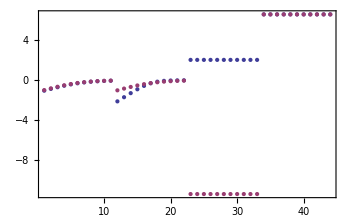

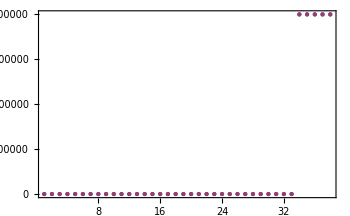

```mathematica
(*Log Space*)
ListPlot[Log10[{vRelData,dataArrayWithSSD[[1,3]]}]]
(*Real Space*)
ListPlot[{vRelData[[;;-7]],dataArrayWithSSD[[1,3,;;-7]]}]
```

### Parameter Distribution

```mathematica
DistributionChart[Transpose[Log10[finalDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Histogram*)
enzymeModel["Reactions"]
```

```mathematica
DistributionChart[Transpose[Log10[finalDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Parameter Analysis and Clustering

#### Remove Redundant Parameter Sets

```mathematica
logError = .5;
Needs["HierarchicalClustering`"]
distMat = DistanceMatrix[Log10[finalDataList[[All,2]]]];
cutoff = Length[finalDataList[[1,2]]]*logError^2;
positionsSimilar = Table[Flatten[Position[distMat[[i]],_?(0< #<cutoff&)]],{i,1,Length[distMat]}];
toRemove = {};
Do[
If[Length[Select[toRemove,#==i&]]==0,
toRemove = Flatten[Append[toRemove,positionsSimilar[[i]]]];],{i,1,Length[positionsSimilar]}];
toRemove = Union[toRemove];
finalDataListRed = finalDataList[[Complement[Table[i,{i,1,Length[finalDataList]}],toRemove]]];
```

#### Cluster Parameters

```mathematica
clusters=FindClusters[Log10[finalDataListRed[[All,2]]],Method->{"Agglomerate","Linkage"->"Complete","SignificanceTest"->{"Gap","Tolerance"->2}}];(**)
medianParamCluster=Table[Median[clusters[[cluster,All,param]]],{cluster,Length[clusters]},{param,Length[clusters[[1,1]]]}](*Switch to log space and use mean?*);
clusterSqdRes=Table[(clusters[[cluster,paramSet,param]]-medianParamCluster[[cluster,param]])^2,{cluster,Length[clusters]},{paramSet,Length[clusters[[cluster]]]},{param,Length[clusters[[1,1]]]}];
clusterSSE=Table[Total[clusterSqdRes[[cluster,paramSet]]],{cluster,Length[clusterSqdRes]},{paramSet,Length[clusterSqdRes[[cluster]]]}];
bestClusterSSE=Table[SortBy[clusterSSE[[cluster]],Less],{cluster,Length[clusterSSE]}][[All,1]];
finalClusterParams={};
Table[If[clusterSSE[[cluster,paramSet]]==bestClusterSSE[[cluster]],finalClusterParams=Append[finalClusterParams,clusters[[cluster,paramSet]]]],{cluster,Length[clusterSSE]},{paramSet,Length[clusterSSE[[cluster]]]}];
```

#### Print Representative Parameter Sets for Each Cluster (Optional)

```mathematica
TableForm[finalClusterParams]
```

### Data Error Distribution

```mathematica
errors=Table[vRelData[[i]]-finalDataList[[j,3,i]],{j,1,Length[finalDataList]},{i,1,Length[finalDataList[[1,3]]]}];
funcNames=Table[StringCases[func,RegularExpression["Development/(.*)\\.txt"]->"$1"][[1]],{func,fittingData[[All,-2]]}];
```

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames](*Histogram*)
```

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartLegends-> funcNames](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*);
```

## Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

### Solving for Km and kcat (using vKm = 1/2 Vmax approach)

```mathematica
paramFitSub=Thread[rateConstsSub[[All,1]]->bestFit[[2]]];
substrFor = getSubstrates[rxn];
substrRev= getProducts[rxn];
cosubsConc={parameter["cosub","atp[c]"]-> 0.001,parameter["cosub","amp[c]"]-> 0.001};

Forward Parameters;
vVal=Table[Simplify[keq2k[absoluteRateForward]/.{substrFor[[i]] -> substrFor[[i]],m_metabolite :> parameter["cosub", ToString@m]}/.paramFitSub/.cosubsConc[[i]]],{i,1,Length[substrFor]}];
vMax=Table[Limit[vVal[[i]],metSatForSub[[i]]],{i,1,Length[substrFor]}];
vKm=Table[Simplify[vVal[[i]] /. met :substrFor[[i]] :> Km[met, KeqName]],{i,1,Length[substrFor]}];
michMentSolForward = Table[Quiet[Solve[vKm[[i]]/vMax[[i]] == 1/2, Km[substrFor[[i]],KeqName]],{Solve::ratnz}],{i,1,Length[substrFor]}];
kcats={Table[rateconst["cat_"<>ToString[substrFor[[i,1]]],True]-> vMax[[i]]/.{parameter["E_total"]-> 1},{i,1,Length[vMax]}]};
michMentSolForward = Join[michMentSolForward,kcats];

Reverse Parameters;
vVal=Table[Simplify[keq2k[absoluteRateReverse]/.{substrRev[[i]] -> substrRev[[i]],m_metabolite :> parameter["cosub", ToString@m]}/.paramFitSub/.cosubsConc[[i]]],{i,1,Length[substrRev]}];
vMax=Table[Limit[vVal[[i]],metSatRevSub[[i]]],{i,1,Length[substrRev]}];
vKm=Table[Simplify[vVal[[i]] /. met :substrRev[[i]] :> Km[met, KeqName]],{i,1,Length[substrRev]}];
michMentSolReverse = Table[Quiet[Solve[vKm[[i]]/vMax[[i]] == 1/2, Km[substrRev[[i]],KeqName]],{Solve::ratnz}],{i,1,Length[substrRev]}];
kcats={Table[rateconst["cat_"<>ToString[substrRev[[i,1]]],True]-> vMax[[i]]/.{parameter["E_total"]-> 1},{i,1,Length[vMax]}]};
michMentSolReverse = Join[michMentSolReverse,kcats];

michMentParams=Flatten[Join[michMentSolForward,michMentSolReverse]];
michMentParams=Select[michMentParams,#[[2]]≥0&];
```

### Comparison to Published Values (*Change to Average +/- StdDev % Error for Each Param*)(*FIXME: Comparison to Published Values*)

```mathematica
michMentParams
```

{K_m_ADK1^(amp^c)→0.000044033,K_m_ADK1^(atp^c)→0.0000460316,k_cat_amp^⟶→1236.55,k_cat_atp^⟶→1239.38,K_m_ADK1^(adp^c)→0.000105475,k_cat_adp^⟶→319.003}

```mathematica
kmListFull[[All,1;;2]]
```

{{adp^c,0.000105},{atp^c,0.000046},{amp^c,0.000044}}

```mathematica
kcatList[[1]]
```

{{{adp,Null}},319.,1/S,7.4,40.}

```mathematica
MapThread[Append,{kcatList[[All,1,All,1]],kcatList[[All,2]]}]
```

{{adp,319.},{amp,atp,1296.}}

```mathematica
parameterData[[All,4]]
```

{Km,kcat,Km,Km,kcat}

```mathematica
"Published Values:"
publishedVals=Thread[michMentParams[[All,1]]->{KmAmp,KmAtp,kcatFor,kcatFor,KmAdp,kcatRev}]
"Fit Values:"
fitVals=michMentParams
Table[(Log10[publishedVals[[i,2]]]-Log10[fitVals[[i,2]]])^2,{i,1,Length[fitVals]}];
"Sum of Squared Log Errors:"
michMentSSE=Total[Table[(Log10[publishedVals[[i,2]]]-Log10[fitVals[[i,2]]])^2,{i,1,Length[fitVals]}]]
```

Published Values:

Thread::tdlen: Objects of unequal length in {InterpretationBox[K_m_StyleBox[ cannot be combined.

{K_m_ADK1^(amp^c),K_m_ADK1^(atp^c),K_m_ADK1^(adp^c)}→{KmAmp,KmAtp,kcatFor,kcatFor,KmAdp,kcatRev}

Fit Values:

{K_m_ADK1^(amp^c)→0.000044033,K_m_ADK1^(atp^c)→0.0000460316,K_m_ADK1^(adp^c)→0.000105475}

Part::partw: Part 3 of {InterpretationBox[K_m_StyleBox[ does not exist.

Sum of Squared Log Errors:

Part::partw: Part 3 of {InterpretationBox[K_m_StyleBox[ does not exist.

(4.33694+Log[KmAtp]/Log[10])^2+(4.35622+Log[K_m_ADK1^(atp^c)]/Log[10])^2+(3.97685+Log[({K_m_ADK1^(amp^c),K_m_ADK1^(atp^c),K_m_ADK1^(adp^c)}→{KmAmp,KmAtp,kcatFor,kcatFor,KmAdp,kcatRev})⟦3,2⟧]/Log[10])^2

{(20 atp^c f6p^c k_PFK11^⟵ k_PFK11^⟶ k_PFK12^⟵ k_PFK13^⟵ k_PFK13^⟶ k_PFK14^⟵ (k_PFK14^⟶ k_PFK15^⟶+((-1/2)^(2/5) k_PFK11^⟶ (k_PFK12^⟶)^2 k_PFK13^⟶ k_PFK14^⟶ k_PFK15^⟶)/(10 k_PFK11^⟵ k_PFK12^⟵ k_PFK13^⟵ k_PFK14^⟵)+k_PFK12^⟶ (k_PFK14^⟶+k_PFK15^⟶)) (k_PFK1_Activation_gdp$11^⟵ k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$11^⟶ (4 k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$12^⟶ (6 k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$13^⟶ (4 k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$14^⟶)))) (k_PFK1_Inhibition_pep^⟵)^4 k_PFK1_TransitionStep^⟵)/((-1)^(2/5) 2^(3/5) f6p^c (k_PFK11^⟶)^2 (k_PFK12^⟶)^2 k_PFK13^⟶ (k_PFK13^⟵+atp^c k_PFK13^⟶) k_PFK14^⟶ k_PFK15^⟶ (k_PFK1_Activation_gdp$11^⟵ k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$11^⟶ (4 k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$12^⟶ (6 k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$13^⟶ (4 k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$14^⟶)))) (k_PFK1_Inhibition_pep^⟵)^4 k_PFK1_TransitionStep^⟵+20 (k_PFK11^⟵)^2 k_PFK12^⟵ k_PFK12^⟶ k_PFK13^⟵ k_PFK14^⟵ k_PFK14^⟶ (k_PFK13^⟵+k_PFK15^⟶) (gdp^c k_PFK1_Activation_gdp$11^⟶ (4 k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$12^⟶ (6 k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$13^⟶ (4 k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$14^⟶))) (k_PFK1_Inhibition_pep^⟵)^4 k_PFK1_TransitionStep^⟵+k_PFK1_Activation_gdp$11^⟵ k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵ (4 pep^c (k_PFK1_Inhibition_pep^⟵)^3 k_PFK1_Inhibition_pep^⟶ k_PFK1_TransitionStep^⟶+6 (pep^c)^2 (k_PFK1_Inhibition_pep^⟵)^2 (k_PFK1_Inhibition_pep^⟶)^2 k_PFK1_TransitionStep^⟶+4 (pep^c)^3 k_PFK1_Inhibition_pep^⟵ (k_PFK1_Inhibition_pep^⟶)^3 k_PFK1_TransitionStep^⟶+(pep^c)^4 (k_PFK1_Inhibition_pep^⟶)^4 k_PFK1_TransitionStep^⟶+(k_PFK1_Inhibition_pep^⟵)^4 (k_PFK1_TransitionStep^⟵+k_PFK1_TransitionStep^⟶)))+k_PFK11^⟵ k_PFK13^⟵ (20 f6p^c k_PFK11^⟶ k_PFK12^⟵ k_PFK14^⟵ (atp^c k_PFK13^⟶ k_PFK14^⟶ k_PFK15^⟶+k_PFK12^⟶ (k_PFK13^⟵ k_PFK14^⟶+k_PFK14^⟶ k_PFK15^⟶+atp^c k_PFK13^⟶ (k_PFK14^⟶+k_PFK15^⟶))) (k_PFK1_Activation_gdp$11^⟵ k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$11^⟶ (4 k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$12^⟶ (6 k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$13^⟶ (4 k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$14^⟶)))) (k_PFK1_Inhibition_pep^⟵)^4 k_PFK1_TransitionStep^⟵+k_PFK12^⟶ k_PFK13^⟶ ((-1)^(2/5) 2^(3/5) k_PFK11^⟶ k_PFK12^⟶+20 atp^c k_PFK12^⟵ k_PFK14^⟵) k_PFK14^⟶ k_PFK15^⟶ (gdp^c k_PFK1_Activation_gdp$11^⟶ (4 k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$12^⟶ (6 k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$13^⟶ (4 k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$14^⟶))) (k_PFK1_Inhibition_pep^⟵)^4 k_PFK1_TransitionStep^⟵+k_PFK1_Activation_gdp$11^⟵ k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵ (4 pep^c (k_PFK1_Inhibition_pep^⟵)^3 k_PFK1_Inhibition_pep^⟶ k_PFK1_TransitionStep^⟶+6 (pep^c)^2 (k_PFK1_Inhibition_pep^⟵)^2 (k_PFK1_Inhibition_pep^⟶)^2 k_PFK1_TransitionStep^⟶+4 (pep^c)^3 k_PFK1_Inhibition_pep^⟵ (k_PFK1_Inhibition_pep^⟶)^3 k_PFK1_TransitionStep^⟶+(pep^c)^4 (k_PFK1_Inhibition_pep^⟶)^4 k_PFK1_TransitionStep^⟶+(k_PFK1_Inhibition_pep^⟵)^4 (k_PFK1_TransitionStep^⟵+k_PFK1_TransitionStep^⟶))))),(20 atp^c f6p^c k_PFK11^⟵ k_PFK11^⟶ k_PFK12^⟵ k_PFK13^⟵ k_PFK13^⟶ k_PFK14^⟵ (k_PFK14^⟶ k_PFK15^⟶+((-1/2)^(2/5) k_PFK11^⟶ (k_PFK12^⟶)^2 k_PFK13^⟶ k_PFK14^⟶ k_PFK15^⟶)/(10 k_PFK11^⟵ k_PFK12^⟵ k_PFK13^⟵ k_PFK14^⟵)+k_PFK12^⟶ (k_PFK14^⟶+k_PFK15^⟶)) (k_PFK1_Activation_gdp$11^⟵ k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$11^⟶ (4 k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$12^⟶ (6 k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$13^⟶ (4 k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$14^⟶)))) (k_PFK1_Inhibition_pep^⟵)^4 k_PFK1_TransitionStep^⟵)/((-1)^(2/5) 2^(3/5) f6p^c (k_PFK11^⟶)^2 (k_PFK12^⟶)^2 k_PFK13^⟶ (k_PFK13^⟵+atp^c k_PFK13^⟶) k_PFK14^⟶ k_PFK15^⟶ (k_PFK1_Activation_gdp$11^⟵ k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$11^⟶ (4 k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$12^⟶ (6 k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$13^⟶ (4 k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$14^⟶)))) (k_PFK1_Inhibition_pep^⟵)^4 k_PFK1_TransitionStep^⟵+20 (k_PFK11^⟵)^2 k_PFK12^⟵ k_PFK12^⟶ k_PFK13^⟵ k_PFK14^⟵ k_PFK14^⟶ (k_PFK13^⟵+k_PFK15^⟶) (gdp^c k_PFK1_Activation_gdp$11^⟶ (4 k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$12^⟶ (6 k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$13^⟶ (4 k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$14^⟶))) (k_PFK1_Inhibition_pep^⟵)^4 k_PFK1_TransitionStep^⟵+k_PFK1_Activation_gdp$11^⟵ k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵ (4 pep^c (k_PFK1_Inhibition_pep^⟵)^3 k_PFK1_Inhibition_pep^⟶ k_PFK1_TransitionStep^⟶+6 (pep^c)^2 (k_PFK1_Inhibition_pep^⟵)^2 (k_PFK1_Inhibition_pep^⟶)^2 k_PFK1_TransitionStep^⟶+4 (pep^c)^3 k_PFK1_Inhibition_pep^⟵ (k_PFK1_Inhibition_pep^⟶)^3 k_PFK1_TransitionStep^⟶+(pep^c)^4 (k_PFK1_Inhibition_pep^⟶)^4 k_PFK1_TransitionStep^⟶+(k_PFK1_Inhibition_pep^⟵)^4 (k_PFK1_TransitionStep^⟵+k_PFK1_TransitionStep^⟶)))+k_PFK11^⟵ k_PFK13^⟵ (20 f6p^c k_PFK11^⟶ k_PFK12^⟵ k_PFK14^⟵ (atp^c k_PFK13^⟶ k_PFK14^⟶ k_PFK15^⟶+k_PFK12^⟶ (k_PFK13^⟵ k_PFK14^⟶+k_PFK14^⟶ k_PFK15^⟶+atp^c k_PFK13^⟶ (k_PFK14^⟶+k_PFK15^⟶))) (k_PFK1_Activation_gdp$11^⟵ k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$11^⟶ (4 k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$12^⟶ (6 k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$13^⟶ (4 k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$14^⟶)))) (k_PFK1_Inhibition_pep^⟵)^4 k_PFK1_TransitionStep^⟵+k_PFK12^⟶ k_PFK13^⟶ ((-1)^(2/5) 2^(3/5) k_PFK11^⟶ k_PFK12^⟶+20 atp^c k_PFK12^⟵ k_PFK14^⟵) k_PFK14^⟶ k_PFK15^⟶ (gdp^c k_PFK1_Activation_gdp$11^⟶ (4 k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$12^⟶ (6 k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$13^⟶ (4 k_PFK1_Activation_gdp$14^⟵+gdp^c k_PFK1_Activation_gdp$14^⟶))) (k_PFK1_Inhibition_pep^⟵)^4 k_PFK1_TransitionStep^⟵+k_PFK1_Activation_gdp$11^⟵ k_PFK1_Activation_gdp$12^⟵ k_PFK1_Activation_gdp$13^⟵ k_PFK1_Activation_gdp$14^⟵ (4 pep^c (k_PFK1_Inhibition_pep^⟵)^3 k_PFK1_Inhibition_pep^⟶ k_PFK1_TransitionStep^⟶+6 (pep^c)^2 (k_PFK1_Inhibition_pep^⟵)^2 (k_PFK1_Inhibition_pep^⟶)^2 k_PFK1_TransitionStep^⟶+4 (pep^c)^3 k_PFK1_Inhibition_pep^⟵ (k_PFK1_Inhibition_pep^⟶)^3 k_PFK1_TransitionStep^⟶+(pep^c)^4 (k_PFK1_Inhibition_pep^⟶)^4 k_PFK1_TransitionStep^⟶+(k_PFK1_Inhibition_pep^⟵)^4 (k_PFK1_TransitionStep^⟵+k_PFK1_TransitionStep^⟶)))))}